## Load packages

### Add notebook directory to package path

```mathematica
AppendTo[$Path,NotebookDirectory[]]
```

{C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\DocumentationIndices,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Kernel,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Autoload,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\Ohdraw.niL,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Data\ICC,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\ChineseSimplified\System\,D:\Ohdraw.niL\OneDrive\Programming\Mathematica\packages_custom,D:\Ohdraw.niL\OneDrive\Programming\Julia\Modules\mathematica_nbs\}

### Initialize

```mathematica
SetDirectory[NotebookDirectory[]<>"/.."];
```

```mathematica
<<PlotMatexFormatting`;
```

```mathematica
<<ExtFileLoading`;
```

```mathematica
<<ArrayManip`;
```

```mathematica
<<FileNamings`;
```

```mathematica
<<StrIOManip`;
```

```mathematica
<<FileSaving`;
```

```mathematica
<<MCLoops`;
```

```mathematica
<<Geo3d`;
```

### Reload external evaluators

```mathematica
<<"ExternalEvaluatorLoad.wl"
```

```mathematica
(*<<"ExternalEvaluateJulia`"*)
```

### Check directory

```mathematica
Directory[]
```

D:\Ohdraw.niL\OneDrive\Programming\Julia\Modules

### Check path

```mathematica
$Path
```

{C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\DocumentationIndices,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Kernel,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Autoload,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\Ohdraw.niL,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Data\ICC,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\ChineseSimplified\System\,D:\Ohdraw.niL\OneDrive\Programming\Mathematica\packages_custom,D:\Ohdraw.niL\OneDrive\Programming\Julia\Modules\mathematica_nbs\}

## File name constants

### Reading

```mathematica
dirLog="./log/";
```

```mathematica
dirFigs="./figs/";
```

```mathematica
dirFigsDoc="./figs/figsDoc/";
```

```mathematica
fNameFLstLstJld2="fNameFileLstJld2Lst.txt";
fNameFLstLst="fNameFileLstLst.txt";
fNameSaveParamLstLst="fNameSaveParamsLst.txt";
```

```mathematica
numDigs=3;
```

### Saving

```mathematica
fNameFigLstTmp="fNameFigLstTmp.txt";
```

## Plotting options

```mathematica
pltOptLstNoStyle={BaseStyle->texStyle,Frame->True,PlotRange->All,PlotRangePadding->{None,Automatic}};
```

```mathematica
pltOptLst={BaseStyle->texStyle,Frame->True,ImageSize->8cm,PlotStyle->lineStyleLstDataThick,PlotRange->All,PlotRangePadding->{None,Automatic}};
```

```mathematica
pltOptMatPlot={BaseStyle->texStyle,Frame->True,PlotRangePadding->None};
```

```mathematica
markerStyleLstTmp=markerStyleLstFunc[colorLst,AbsolutePointSize[4]];
```

```mathematica
markerStyleLstLine=markerStyleLstFunc[colorLst,AbsolutePointSize[2]];
```

```mathematica
markerStyleLstOpac=markerStyleLstFunc[Opacity[0.3,#]&/@colorLst,AbsolutePointSize[3]];
```

## Convergence check functions

### MapThread function

```mathematica
optFunIsItLst={"IsItLst"->False};
Options[mapThreadPart]={"NumRegArg"->0};
mapThreadPart[fun_,argSeq__,OptionsPattern[]]:=
Module[{numRegArg=OptionValue["NumRegArg"],argLst={argSeq}},
MapThread[fun[Sequence@@argLst⟦1;;numRegArg⟧,##]&,argLst⟦numRegArg+1;;-1⟧]
];
(*funOrgAndMapped[fun_,OptionsPattern[]]:=
(If[OptionValue["IsItLst"],
mapThreadPart[fun,##,"NumRegArg"->OptionValue["NumRegAr"]],
fun[##]
])&;*)
Options[funOrgAndMapped]=Options[mapThreadPart];
funOrgAndMapped[fun_,OptionsPattern[]]:=
Module[{funMapped,numRegArg=OptionValue["NumRegArg"]},
Options[funMapped]=optFunIsItLst;
funMapped[argLst__,OptionsPattern[]]:=
If[OptionValue["IsItLst"],
mapThreadPart[fun,argLst,"NumRegArg"->numRegArg],
fun[argLst]
];
funMapped
]
Options[funOrgAndThreadedArr]=Options[mapThreadPart];
funOrgAndThreadedArr[fun_,OptionsPattern[]]:=
Module[{funMapped,numRegArg=OptionValue["NumRegArg"]},
Options[funMapped]=optFunIsItLst;
funMapped[argLst__,OptionsPattern[]]:=
If[OptionValue["IsItLst"],
Transpose[mapThreadPart[fun,argLst,"NumRegArg"->numRegArg],Reverse[Range[2]]],
fun[argLst]
];
funMapped
]
```

```mathematica
(*funMapped[argLst__,OptionsPattern[]]:=
If[OptionValue["IsItLst"],
mapThreadPart[fun,argLst,"NumRegArg"->OptionValue["NumRegAr"]]&,
fun[argLst]
];*)
```

### Filename and variables loading functions

```mathematica
getFNameArrGrpLst[fNameFLstJld2_]:=
Module[{fNameFLstJld2Lst=readJuliaVar[fNameFLstJld2,"fLstNameLst"]},
Table[readJuliaVarDimRev[fNameFLstJld2Lst⟦iGrp⟧,"fNameArr"],{iGrp,Length[fNameFLstJld2Lst]}]
];
(*getFNameArrGrpItNumLst[fNameFLst_]:=MapThread[getFNameArrGrpLst,{fNameFLst}];*)
(*getFNameArrGrpItNumLst[fNameFLstRoot_]:=
Module[{fNameFLstJld2MasterLst=readJuliaVar[fNameFLstRoot,"fLstJld2MasterNameLst"]},
fNameFLstItNums=Table[getFNameArrGrpLst[fNameFLstJld2MasterLst⟦iIt⟧],{iIt,Length[fNameFLstJld2MasterLst]}];
];*)
getFNameArrGrpItNumLst[fNameFLstRoot_]:=
Module[{fNameFLstJld2MasterLst=readJuliaVar[fNameFLstRoot,"fLstJld2MasterNameLst"]},
MapThread[getFNameArrGrpLst,{fNameFLstJld2MasterLst}]
];
Options[getFNameArrLst]=optFunIsItLst;
getFNameArrLst[fNameFLstRoot_,OptionsPattern[]]:=
If[OptionValue["IsItLst"],
getFNameArrGrpItNumLst[fNameFLstRoot],
getFNameArrGrpLst[fNameFLstRoot]
]
```

```mathematica
getLttcParams[fNameParams_]:=
readJuliaVar[fNameParams,#]&/@{"itNumLst","divNumLst","isInit0Lst"};
(*Module[{itNumLst,divNumLst,isInit0Lst},
If[OptionValue["IsItLst"],
{itNumLst,divNumLst,isInit0Lst}=readJuliaVar[fNameParams,#]&/@{"itNumLst","divNumLst","isInit0Lst"};
,
readJuliaVarDimRev[fNameParams,#]&/@{"itNumLst","divNumLst","isInit0Lst"};
]
]*)
```

```mathematica
(*{itNumLst,divNumLst,isInit0Lst}=readJuliaVarDimRev[fNameParams,#]&/@{"itNumLst","divNumLst","isInit0Lst"};*)
getGrpParamsNameLst[fNameParams_]:=readJuliaVar[fNameParams,#]&/@{"grpNameLst","grpParamsLst","grpParamsNameLst"};
(*{grpNameLst,grpParamsLst,grpParamsNameLst}=readJuliaVar[fNameParams,#]&/@{"grpNameLst","grpParamsLst","grpParamsNameLst"};
{cAreaLstRaw,cPerimLstRaw,cFerroLstRaw}=readJuliaVar[fNameParams,#]&/@{"cAreaLst","cPerimLst","cFerroLst"};*)
```

```mathematica
Options[getCParams]=optFunIsItLst;
getCParamsBundled=funOrgAndMapped[{##}&];
getCParams[fNameParams_,OptionsPattern[]]:=
Module[{cAreaLstRaw,cPerimLstRaw,cFerroLstRaw},
{cAreaLstRaw,cPerimLstRaw,cFerroLstRaw}=readJuliaVar[fNameParams,#]&/@{"cAreaLst","cPerimLst","cFerroLst"};
If[OptionValue["IsItLst"],
(vectOfArrReverseDims/@#)&/@{cAreaLstRaw,cPerimLstRaw,cFerroLstRaw},
vectOfArrReverseDims/@{cAreaLstRaw,cPerimLstRaw,cFerroLstRaw}
]
];
```

```mathematica
(*cParamsDimRevGrpLst[cAreaLstRaw_,cPerimLstRaw_,cFerroLstRaw_]:=vectOfArrReverseDims/@{cAreaLstRaw,cPerimLstRaw,cFerroLstRaw};
cParamsDimRevGrpItNumLst[cAreaLstRaw_,cPerimLstRaw_,cFerroLstRaw_]:=
(vectOfArrReverseDims/@#)&/@{cAreaLstRaw,cPerimLstRaw,cFerroLstRaw};*)
```

```mathematica
(*{cAreaLst,cPerimLst,cFerroLst}=vectOfArrReverseDims/@{cAreaLstRaw,cPerimLstRaw,cFerroLstRaw};*)
```

```mathematica
getIterGrpLst[grpParamsLst_]:=
Module[{iGrpParamsLst,iGrpParamsBndLst},
iGrpParamsLst=Table[Table[iPrm[iGrp,iIt],{iIt,Length[grpParamsLst⟦iGrp⟧]}],{iGrp,Length[grpParamsLst]}];
iGrpParamsBndLst=Table[Table[{iGrpParamsLst⟦iGrp,iIt⟧,Length[grpParamsLst⟦iGrp,iIt⟧]},{iIt,Length[grpParamsLst⟦iGrp⟧]}],{iGrp,Length[grpParamsLst]}];
{iGrpParamsLst,iGrpParamsBndLst}
];
getIterLst=funOrgAndThreadedArr[getIterGrpLst];
(*getIterGrpItLst[argLst_]:=Transpose[MapThread[getIterGrpLst,{argLst}],Reverse[Range[2]]];
getIterGrpItLst[grpParamsLst_,grpParamsNameLst_]:=
Module[{iGrpParamsLsts=ConstantArray[0,Length[grpParamsLst]],iGrpParmasBndLsts=ConstantArray[0,Length[grpParamsLst]]},
Do[{iGrpParamsLsts⟦iIt⟧,iGrpParamsBndLst⟦iIt⟧}=getIterGrpLst[grpParamsLst⟦iIt⟧,grpParamsNameLst⟦iIt⟧],{iIt,Length[grpParamsLst]}];
];*)
```

```mathematica
getIterLatticeGrpLst[divNumLst_,isInit0Lst_,itNumLst_]:=
Module[{paramLttcLst={itNumLst,divNumLst,isInit0Lst},iLttcLst,iBndLttcLst},
iLttcLst=Table[iLttc[iPrmLttc],{iPrmLttc,Length[paramLttcLst]}];
iBndLttcLst=Table[{iLttcLst⟦iPrmLttc⟧,Length[paramLttcLst⟦iPrmLttc⟧]},{iPrmLttc,Length[paramLttcLst]}];
{iLttcLst,iBndLttcLst}
];
getIterLatticeLst=funOrgAndThreadedArr[getIterLatticeGrpLst,"NumRegArg"->2];
```

```mathematica
getIterLatticeItGrpLst[divNumLst_,isInit0Lst_,itNumLst_]:=MapThread[getIterLatticeLst[##,divNumLst,isInit0Lst]&,{itNumLst}];
```

```mathematica
getLatticeParamGrpLst[divNumLst_,isInit0Lst_,itNumLst_]:={itNumLst,divNumLst,isInit0Lst};
getLatticeParamLst=funOrgAndMapped[getLatticeParamGrpLst,"NumRegArg"->2];
```

```mathematica
getNumGrdLst[nDim_,divNumLst_]:=divNumLst^nDim;
```

```mathematica
getLatticeParamItLst[divNumLst_,isInit0Lst_,itNumLst_]:=MapThread[getLatticeParamLst[##,divNumLst,isInit0Lst]&,{itNumLst}];
```

### cParams 2d functions

```mathematica
c2dLstFunGrpLst[cAreaLst_,cPerimLst_]:=Table[Transpose[{cAreaLst⟦iGrp⟧,cPerimLst⟦iGrp⟧},{ArrayDepth[cAreaLst⟦iGrp⟧]+1}~Join~Range[1,ArrayDepth[cAreaLst⟦iGrp⟧]]],{iGrp,Length[cAreaLst]}];
c2dLstFun=funOrgAndMapped[c2dLstFunGrpLst];
```

```mathematica
c2dLstFunGrpItNumLst[argLst__]:=
MapThread[c2dLstFunGrpLst,{argLst}];
(*Table[c2dLstFunGrpLst[cAreaLst⟦iIt⟧,cPerimLst⟦iIt⟧],{iIt,Length[cAreaLst]}];*)
```

### load files

```mathematica
(*loadGrpLstArr[fNameArr_,varName_,itNumLst_,divNumLst_,isInit0Lst_,iGrpParamsLst_]:=Table[Table[readJuliaVar[fNameArr⟦iGrp⟧⟦iIt,iDiv,iInit,Sequence@@iGrpParamsLst⟦iGrp⟧⟧,varName],{iDiv,Length[divNumLst]},{iIt,Length[itNumLst]},{iInit,Length[isInit0Lst]},Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧]],{iGrp,Length[fNameArr]}];*)
loadGrpLstArr[varName_,fNameArr_,iGrpParamsLst_,iGrpParamsBndLst_,iLttcLst_,iBndLttcLst_]:=Table[Table[readJuliaVar[fNameArr⟦iGrp⟧⟦Sequence@@iLttcLst,Sequence@@iGrpParamsLst⟦iGrp⟧⟧,varName],Evaluate[Sequence@@iBndLttcLst],Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧]],{iGrp,Length[fNameArr]}];
loadLstArr=funOrgAndMapped[loadGrpLstArr,"NumRegArg"->1];
(*loadGrpItNumLstArr[varName_,fNameArr_,iGrpParamsLst_,iGrpParamsBndLst_,iLttcLst_,iBndLttcLst_]:=
Table[loadGrpLstArr[fNameArr⟦iIt⟧,varName,itNumLst⟦iIt⟧],{iIt,Length[fNameArr]}];*)
```

```mathematica
normalizeArrGrpLst[numGrdLst_,arr_,iGrpParamsLst_,iLttcLst_,iBndLttcLst_]:=
Table[Table[arr⟦iGrp,Sequence@@iLttcLst⟧/numGrdLst⟦iLttcLst⟦2⟧⟧,Evaluate[Sequence@@iBndLttcLst]],{iGrp,Length[iGrpParamsLst]}];
normalizeArr=funOrgAndMapped[normalizeArrGrpLst,"NumRegArg"->1];
```

```mathematica
loadGrpItNumLstArr[varName_,fNameArr_,iGrpParamsLst_,iGrpParamsBndLst_,iLttcLst_,iBndLttcLst_]:=
MapThread[loadGrpLstArr[varName,##]&,{fNameArr,iGrpParamsLst,iGrpParamsBndLst,iLttcLst,iBndLttcLst}];
```

### average functions

```mathematica
avgArrGrpLstTail[itAvgStart_,arr_]:=
Table[
Map[Mean,
Map[Mean[#⟦-itAvgStart;;-1⟧]&,arr⟦iGrp⟧,{ArrayDepth[arr⟦iGrp⟧]-1}],
{ArrayDepth[arr⟦iGrp⟧]-2}],
{iGrp,Length[arr]}];
avgArrLstTail=funOrgAndMapped[avgArrGrpLstTail,"NumRegArg"->1];
```

```mathematica
avgArrGrpLstTail2[itAvgStart_,arr_]:=
Table[
Map[Mean[#⟦-itAvgStart;;-1⟧]&,arr⟦iGrp⟧,{ArrayDepth[arr⟦iGrp⟧]-1}],
{iGrp,Length[arr]}];
avgArrLstTail2=funOrgAndMapped[avgArrGrpLstTail2,"NumRegArg"->1];
```

### plot titles

```mathematica
paramStrLst={"c_A","c_L", "c_F"};
```

```mathematica
titleFigLstRawGrpLstFun[cAreaLst_,cPerimLst_,cFerroLst_,iGrpParamsLst_,iGrpParamsBndLst_]:=
Table[
Table[
Module[{valLst},
valLst={cAreaLst⟦iGrp⟧⟦##⟧,cPerimLst⟦iGrp⟧⟦##⟧,cFerroLst⟦iGrp⟧⟦##⟧}&@@iGrpParamsLst⟦iGrp⟧;
titleParamLstGen[paramStrLst,floatToStrWith0[#,numDigs]&/@valLst]
]
,Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧]]
,{iGrp,Length[cAreaLst]}];
titleFigLstRawLstFun=funOrgAndMapped[titleFigLstRawGrpLstFun];
```

```mathematica
titleFigLstRawGrpItNumLstFun[argLst_]:=
MapThread[titleFigLstRawGrpLstFun,{argLst}];
(*Table[
titleFigLstRawGrpLstFun[cAreaLst,cPerimLst,cFerroLst]=
,{iIt,Length[cAreaLst]}];*)
```

### plotting listplots

```mathematica
(*pltLstPltGrpLst[arr_,titleLst_,itNumLst_]:=
Table[
Table[ListPlot[arr⟦iGrp⟧⟦iIt,iDiv,iInit,Evaluate@Sequence@@iGrpParamsLst⟦iGrp⟧,iDim⟧/numGrd,pltOptLstNoStyle,PlotStyle->markerStyleLstTmp,ImageSize->8cm,PlotLabel->titleLst⟦iGrp⟧⟦Sequence@@iGrpParamsLst⟦iGrp⟧⟧,FrameLabel->xyLabBLnkLst⟦1,iDim⟧],{iIt,Length[itNumLst]},{iDiv,Length[divNumLst]},{iInit,Length[isInit0Lst]},Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧],{iDim,3}]
,{iGrp,Length[arr]}];*)
pltLstPltGrpLst[arr_,titleLst_,iGrpParamsLst_,iGrpParamsBndLst_,iLttcLst_,iBndLttcLst_]:=
Table[
Table[ListPlot[arr⟦iGrp⟧⟦Sequence@@iLttcLst,Sequence@@iGrpParamsLst⟦iGrp⟧,iDim⟧,pltOptLstNoStyle,PlotStyle->markerStyleLstLine,ImageSize->8cm,PlotLabel->titleLst⟦iGrp⟧⟦Sequence@@iGrpParamsLst⟦iGrp⟧⟧,FrameLabel->xyLabBLnkLst⟦1,iDim⟧],Evaluate[Sequence@@iBndLttcLst],Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧],{iDim,3}]
,{iGrp,Length[arr]}];
pltLstFun=funOrgAndMapped[pltLstPltGrpLst];
(*pltLstPltGrpLst[arr_,titleLst_,iGrpParamsLst_,iGrpParamsBndLst_,iLttcLst_,iBndLttcLst_]:=
Table[
pltLstPltGrpLst[arr⟦iIt⟧,titleLst⟦iIt⟧,itNumLst⟦iIt⟧]
,{iIt,Length[arr]}];*)
```

```mathematica
pltLstPltGrpItLst[argLst__]:=
MapThread[pltLstPltGrpLst,{argLst}];
```

### plots fileNames

```mathematica
(*fNameJpgLstGrpLstFun[fMain_,lttcParamLst_,iGrpParamsLst_,iGrpParamsBndLst_,iLttcLst_,iBndLttcLst_]:=Table[
Table[
Module[{valLst,fName},
valLst=(floatToStrWith0[#,numDigs]&/@({cAreaLst⟦iGrp,##⟧,cPerimLst⟦iGrp,##⟧,cFerroLst⟦iGrp,##⟧}&@@ iGrpParamsLst⟦iGrp⟧))~Join~{itNumLst⟦iIt⟧,divNumLst⟦iDiv⟧,isInit0Lst⟦iInit⟧}~Join~{iDim};
fNameFun[fMain,attrLstLoopsMCFig,valLst,jpgType]
],
Evaluate[Sequence@@iBndLttcLst],Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧],{iDim,nDim}]
,{iGrp,Length[grpNameLst]}];*)
fNameJpgLstGrpLstFun[fMain_,cParamLst_,lttcParamLst_,iGrpParamsLst_,iGrpParamsBndLst_,iLttcLst_,iBndLttcLst_]:=Table[
Table[
Module[{valLst,fName},
valLst=(floatToStrWith0[#,numDigs]&/@(#⟦iGrp,Sequence@@iGrpParamsLst⟦iGrp⟧⟧&/@cParamLst))~Join~MapThread[#1⟦#2⟧&,{lttcParamLst,iLttcLst}]~Join~{iDim};
fNameFun[fMain,attrLstLoopsMCFig,valLst,jpgType]
],
Evaluate[Sequence@@iBndLttcLst],Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧],{iDim,nDim}]
,{iGrp,Length[iGrpParamsLst]}];
fNameJpgLstFun=funOrgAndMapped[fNameJpgLstGrpLstFun,"NumRegArg"->1];
```

```mathematica
(*fNameJpgLstGrpItNumLstFun[fMain_,iterLsts__]:=
Table[
fNameJpgLstGrpLstFun[fMain,itNumLst⟦iIt⟧];
,{iIt,Length[grpNameLst]}];*)
fNameJpgLstGrpItNumLstFun[fMain_,iterLsts__]:=
MapThread[fNameJpgLstGrpNumLstFun[fMain,##]&,{iterLsts}];
```

```mathematica
(*exportPltsGrpLstFun[arr_,fNameLst_,itNumLst_]:=
Do[
Do[
Export[dirFig<>fNameFigNumBfieldJpgLst⟦iGrp,iIt,iDiv,iInit,Sequence@@iGrpParamsLst⟦iGrp⟧,iDim⟧,pltLstNumBfield⟦iGrp,iIt,iDiv,iInit,Sequence@@iGrpParamsLst⟦iGrp⟧,iDim⟧]
,{iIt,Length[itNumLst]},{iDiv,Length[divNumLst]},{iInit,Length[isInit0Lst]},Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧],{iDim,nDim}],
{iGrp,Length[arr]}];*)
exportPltGrpLstFun[fNameLst_,pltLst_,iGrpParamsLst_,iGrpParamsBndLst_,iLttcLst_,iBndLttcLst_]:=
Do[
ParallelDo[
Export[dirFigs<>fNameLst⟦iGrp,Sequence@@iLttcLst,Sequence@@iGrpParamsLst⟦iGrp⟧,iDim⟧,pltLst⟦iGrp,Sequence@@iLttcLst,Sequence@@iGrpParamsLst⟦iGrp⟧,iDim⟧],Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧],{iDim,nDim},
DistributedContexts->Automatic],
Evaluate[Sequence@@iBndLttcLst],{iGrp,Length[iGrpParamsLst]}];
exportPltLstFun=funOrgAndMapped[exportPltGrpLstFun];
```

```mathematica
(*exportPltsGrpItNumLstFun[arr_,fNameLst_,itNumLst_]:=
Do[
exportPltsGrpLstFun[arr⟦iIt⟧,fNameLst⟦iIt⟧,itNumLst⟦iIt⟧]
,{iIt,Length[iIt]}];*)
exportPltsGrpItNumLstFun[argLst_]:=
MapThread[exportPltGrpLstFun,{argLst}];
```

## Convergence check with func

### Load files

```mathematica
isItLst=False;
```

```mathematica
fNameFLstJld2=readTxtLastLine[dirLog<>fNameFLstLstJld2];
fNameParams=readTxtLastLine[dirLog<>fNameSaveParamLstLst];
```

```mathematica
fNameArr=getFNameArrLst[fNameFLstJld2,"IsItLst"->isItLst];
```

```mathematica
Dimensions/@fNameArr
```

{{1,1,4,1,1}}

```mathematica
{itNumLst,divNumLst,isInit0Lst}=getLttcParams[fNameParams];
```

```mathematica
itNumLst
```

{{10000},{2000}}

```mathematica
grpParamsTest=readJuliaVar["testSave.jld2","grpParamsLst"];
```

```mathematica
grpParamsTest
```

{{{0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.},{0.942478,1.25664},{0.},{1.},{1.}}}

```mathematica
fNameParams
```

loopsMC_params_div_64_it_10_nDim_3_cRadius_[0.6, 0.8]_cAngle_[0.942, 1.257]_cFerroRatio_0_sgnAreaLst_1_sgnPerimLst_1_cAreas_-7_cPerims_[-1, -3]_cFerros_0_upStagCube.jld2

```mathematica
divNumLst
```

{64}

```mathematica
isInit0Lst
```

{False}

```mathematica
fNameArr⟦1⟧//Dimensions
```

{1,1,1,15,4,1,1,1}

```mathematica
{grpNameLst,grpParamsLst,grpParamsNameLst}=getGrpParamsNameLst[fNameParams];
```

```mathematica
{cAreaLst,cPerimLst,cFerroLst}=getCParams[fNameParams,"IsItLst"->isItLst];
cParamLst=getCParamsBundled[cAreaLst,cPerimLst,cFerroLst,"IsItLst"->isItLst];
```

```mathematica
Dimensions/@cParamLst
```

{{3,1,13,2,1,1,1},{3,3,15,1,1}}

```mathematica
{iCParamLst,iBndCParamLst}=getIterLst[grpParamsLst,"IsItLst"->isItLst];
```

```mathematica
{iLttcLst,iBndLttcLst}=getIterLatticeLst[divNumLst,isInit0Lst,itNumLst,"IsItLst"->isItLst];
```

```mathematica
lttcParamLst=getLatticeParamLst[divNumLst,isInit0Lst,itNumLst,"IsItLst"->isItLst];
```

```mathematica
nDim=3;
```

```mathematica
numGrdLst=getNumGrdLst[nDim,divNumLst];
```

```mathematica
iLttcLst
```

{{iLttc[1],iLttc[2],iLttc[3]},{iLttc[1],iLttc[2],iLttc[3]}}

```mathematica
c2dLst=c2dLstFun[cAreaLst,cPerimLst,"IsItLst"->isItLst];
```

```mathematica
Dimensions/@c2dLst
```

{{1,13,2,1,1,1,2},{3,15,1,1,2}}

```mathematica
c2dLstGrp=Join@@MapThread[Flatten,{c2dLst,{{{3},{1,2}~Join~Range[4,6]},{{1},Range[2,4]}}}];
```

```mathematica
Dimensions/@c2dLstGrp
```

{{120},{6},{6},{6},{6},{6},{6},{6},{6},{6},{6},{6},{6},{6},{6},{6}}

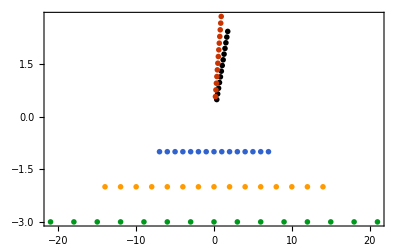

```mathematica
ListPlot[c2dLstGrp,pltOptLstNoStyle,PlotStyle->markerStyleLstTmp,FrameLabel->xyLabscAcL]
```

```mathematica
(*c2dLstGrp=Join@@MapThread[Flatten,{c2dLst,{{{2},{1}~Join~Range[3,5]},{{2},{1,3}}}}];*)
```

```mathematica
{numBfieldLstArr,numLinkLstArr}=loadLstArr[#,fNameArr,iCParamLst,iBndCParamLst,iLttcLst,iBndLttcLst,"IsItLst"->isItLst]&/@{"numBfieldLst","numLinkLst"};
```

```mathematica
Dimensions/@numBfieldLstArr
```

{{1,1,1,1,13,2,1,1,1,3,10000},{3,1,1,1,15,1,1,3,2000}}

```mathematica
{numBfieldLstArrNormed,numLinkLstArrNormed}=normalizeArr[numGrdLst,#,iCParamLst,iLttcLst,iBndLttcLst,"IsItLst"->isItLst]&/@{numBfieldLstArr,numLinkLstArr};
```

```mathematica
itAvgStart=200;
{numBfieldAvgArr,numLinkAvgArr}=avgArrLstTail[itAvgStart,#,"IsItLst"->isItLst]&/@{numBfieldLstArrNormed,numLinkLstArrNormed};
```

```mathematica
Dimensions/@numBfieldAvgArr
```

{{1,1,1,1,13,2,1,1,1},{3,1,1,1,15,1,1}}

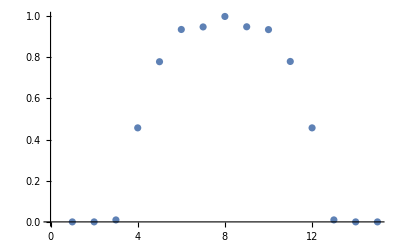

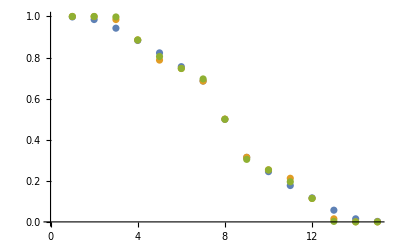

```mathematica
ListPlot[numLinkAvgArr⟦2,3,1,1,1,All,1,1⟧]
```

```mathematica
Dimensions/@numBfieldLstArrNormed
```

{{1,1,1,1,13,2,1,1,1,3,10000},{3,1,1,1,15,1,1,3,2000}}

### Plotting params and file names

#### file naming

```mathematica
fMainLoopMCFig="loopsMC";
fMainLoopMCFigBfield=fMainLoopMCFig<>"Bfield";
fMainLoopMCFigLink=fMainLoopMCFig<>"Link";
fMainLoopMCFigBfLnk=fMainLoopMCFig<>"BfLnk";
fMainLoopMCFigBfieldAllDim=fMainLoopMCFigBfield<>"AllDim";
fMainLoopMCFigLinkAllDim=fMainLoopMCFigLink<>"AllDim";
```

```mathematica
fNamefNameFigLstTmp="fNameFigLstTmp.txt";
```

```mathematica
attrLstSimSetup={"itNum","divNum","isInit0"};
attrLstParams={"cArea","cPerim", "cFerro"};
attrLstBase=attrLstParams~Join~attrLstSimSetup;
attrLstItCut={"itCut"};
attrLstIDim={"iDim"};
```

```mathematica
(*attrLstLoopsMCFig={"cArea","cPerim", "cFerro", "isInit0","iDim","itCut"};*)
```

```mathematica
attrLstLoopsMCFig=attrLstBase~Join~attrLstIDim;
attrLstLoopsMCFigCut=attrLstBase~Join~attrLstIDim~Join~attrLstItCut;
```

#### Axis label

```mathematica
xyLabscAcL=matexLstFunc[{"c_A","c_L"},labMag];
```

```mathematica
itCut=10000;
```

```mathematica
itCut=-1;
```

```mathematica
varTrackedLstRaw={"s","\\ell"};
```

```mathematica
dimLabLst={"x","y","z"};
```

```mathematica
itLab="\\mathrm{iteration}";
```

```mathematica
xyLabNoDimLstRaw=Table[{itLab,"\\langle "<>varTrackedLstRaw⟦iBL⟧<>" \\rangle"},{iBL,2}];
```

```mathematica
xyLabNoDimLst=matexLstFunc[xyLabNoDimLstRaw,labMag];
```

```mathematica
xyLabNoDimLst
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
xyLabNoDimLst⟦All,2⟧
```

{-Graphics-,-Graphics-}

```mathematica
xyLabBLnkLstRaw=Table[{itLab,"\\langle "<>varTrackedLstRaw⟦iBL⟧<>"_"<>dimLabLst⟦iDim⟧<>" \\rangle"},{iBL,2},{iDim,nDim}];
```

```mathematica
xyLabBLnkLst=matexLstFunc[xyLabBLnkLstRaw,labMag];
```

```mathematica
xyLabBLnkLst
```

{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}

```mathematica
xyLabBLnkLst⟦All,All,2⟧
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

Test label output

```mathematica
xyLabNoDimLst
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
xyLabBLnkLst
```

{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}

```mathematica
xyLabThetaDimLstRaw=Table["\\theta"<>"_"<>dimLabLst⟦iDim⟧,{iDim,nDim}];
```

```mathematica
xyLabThetaDimNormedLstRaw=(#<>" / 2 \\pi") &/@xyLabThetaDimLstRaw;
```

```mathematica
xyLabThetaDimLst=matexLstFunc[xyLabThetaDimLstRaw,labMag];
```

```mathematica
xyLabThetaDimNormedLst=matexLstFunc[xyLabThetaDimNormedLstRaw,labMag];
```

```mathematica
xyLabThetaDimNormedLst
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
xyLabThetaDimLst
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
xyLabTheta2dLst=Table[Delete[xyLabThetaDimLst,iDim],{iDim,nDim}];
```

```mathematica
xyLabTheta2dNormedLst=Table[Delete[xyLabThetaDimNormedLst,iDim],{iDim,nDim}];
```

```mathematica
xyLabTheta2dNormedLst
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
xyLabTheta2dLst
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
cAreaLst//Dimensions
```

{}

#### Title

```mathematica
titleLstRaw=titleFigLstRawLstFun[cAreaLst,cPerimLst,cFerroLst,iCParamLst,iBndCParamLst,"IsItLst"->isItLst];
```

```mathematica
Dimensions/@titleLstRaw
```

{{1,13,2,1,1,1},{3,15,1,1}}

```mathematica
titleLstMatex=matexLstFunc[titleLstRaw,labMag];
```

### Plotting

```mathematica
{pltBfieldLst,pltLinkLst}=pltLstFun[#,titleLstMatex,iCParamLst,iBndCParamLst,iLttcLst,iBndLttcLst,"IsItLst"->isItLst]&/@{numBfieldLstArrNormed,numLinkLstArrNormed};
```

```mathematica
{fNamePltLstBfield,fNamePltLstLink}=fNameJpgLstFun[#,cParamLst,lttcParamLst,iCParamLst,iBndCParamLst,iLttcLst,iBndLttcLst,"IsItLst"->isItLst]&/@{fMainLoopMCFigBfield,fMainLoopMCFigLink};
```

```mathematica
Dimensions/@fNamePltLstBfield
```

{{1,1,1,1,13,2,1,1,1,3},{3,1,1,1,15,1,1,3}}

```mathematica
fNamePltLstBfield⟦1,1,1,1,1,1,1,1,1,1,1⟧
```

loopsMCBfield_cArea_0.353_cPerim_0.485_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg

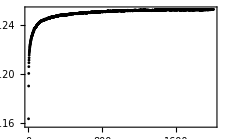

```mathematica
pltBfieldLst⟦2,2,1,1,1,10,1,1,2⟧
```

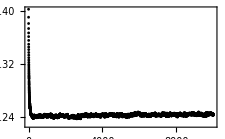

```mathematica
pltBfieldLst⟦1,1,1,1,1,1,1,1,1,1,1⟧
```

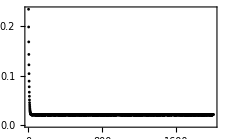

```mathematica
ListPlot[numBfieldLstArrNormed⟦1,1,1,1,5,1,1,1,1,1⟧,pltOptLstNoStyle,PlotStyle->markerStyleLstLine,ImageSize->8cm,FrameLabel->xyLabBLnkLst⟦1,3⟧]
```

### Export plots

```mathematica
nII=15;
nJJ=4;
AbsoluteTiming[Do[Export[dirFigs<>"testFig"<>ToString[ii]<>".jpg",pltBfieldLst⟦1,1,1,1,ii,jj,1,1,1,1⟧,"JPEG"],{ii,nII},{jj,nJJ}]]
AbsoluteTiming[ParallelDo[Export[dirFigs<>"testFig"<>ToString[ii]<>".jpg",pltBfieldLst⟦1,1,1,1,ii,2,1,1,1,1⟧,"JPEG"],{ii,nII},{jj,nJJ},DistributedContexts->Automatic]]
```

{373.856,Null}

{30.2638,Null}

```mathematica
nII=15;
nJJ=1;
AbsoluteTiming[ParallelDo[Export[dirFigs<>"testFig"<>ToString[ii]<>".jpg",pltBfieldLst⟦1,1,1,1,ii,2,1,1,1,1⟧],{ii,nII},{jj,nJJ},DistributedContexts->Automatic]]
AbsoluteTiming[ParallelDo[Export[dirFigs<>"testFig"<>ToString[ii]<>".jpg",pltBfieldLst⟦1,1,1,1,ii,2,1,1,1,1⟧,"JPEG"],{ii,nII},{jj,nJJ},DistributedContexts->Automatic]]
```

{9.89461,Null}

{9.48802,Null}

```mathematica
AbsoluteTiming[exportPltLstFun[fNamePltLstBfield,pltBfieldLst,iCParamLst,iBndCParamLst,iLttcLst,iBndLttcLst,"IsItLst"->isItLst]]
```

{8.19329,{Null,Null}}

```mathematica
AbsoluteTiming[MapThread[exportPltLstFun[#1,#2,iCParamLst,iBndCParamLst,iLttcLst,iBndLttcLst,"IsItLst"->isItLst]&,{{fNamePltLstBfield,fNamePltLstLink},{pltBfieldLst,pltLinkLst}}]]
```

{2615.58,{{Null,Null},{Null,Null}}}

### Fig files moving

```mathematica
Dimensions/@fNamePltLstBfield
```

{{1,1,1,1,13,2,1,1,1,3},{3,1,1,1,15,1,1,3}}

```mathematica
fNamePltLstBfield⟦1,1,1,1,1,All,1,1,1,1,1⟧
```

{loopsMCBfield_cArea_0.353_cPerim_0.485_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_0.470_cPerim_0.647_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_0.588_cPerim_0.809_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_0.705_cPerim_0.971_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_0.823_cPerim_1.133_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_0.940_cPerim_1.294_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_1.058_cPerim_1.456_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_1.176_cPerim_1.618_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_1.293_cPerim_1.780_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_1.411_cPerim_1.942_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_1.528_cPerim_2.103_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_1.646_cPerim_2.265_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_1.763_cPerim_2.427_cFerro_0_itNum_10000_divNum_64_isInit0_False_iDim_1.jpg}

```mathematica
saveStrLstDelim[dirFigs<>fNameFigLstTmp,fNamePltLstBfield⟦1,1,1,1,1,All,1,1,1,1,1⟧];
```

### Plot s, l against cParams

#### xyLabs

```mathematica
cRadiusLab=matexLstFunc[{"\\sqrt{c_A^2 + c_L^2}"},labMag];
```

```mathematica
cRadiusLab
```

{-Graphics-}

```mathematica
cALab=matexLstFunc[{"c_A"},labMag];
```

```mathematica
cALab
```

{-Graphics-}

```mathematica
grpParamsLst⟦2⟧
```

{{-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.},{-1.,-2.,-3.},{0.}}

```mathematica
ToString@@grpParamsLst⟦2,2⟧
```

ToString::nonopt: Options expected (instead of -3.) beyond position 2 in ToString[-1.,-2.,-3.]. An option must be a rule or a list of rules.

ToString[-1.,-2.,-3.]

```mathematica
ToString
```

```mathematica
legTitleCP=MaTeX["c_L=",Magnification->labMag];
```

```mathematica
legTitleCP
```

-Graphics-

```mathematica
legLabLstCP=matexLstFunc[ToString/@grpParamsLst⟦2,2⟧,labMag]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
angleLst=grpParamsLst⟦1,2⟧/π
```

{0.1,0.2,0.3,0.4}

```mathematica
legTitleAngle=MaTeX["\\tan^{-1} c_L / c_A =",Magnification->labMag]
```

-Graphics-

```mathematica
legLabLstAngle=matexLstFunc[ToString[#]<>"\\pi"&/@angleLst,labMag]
```

StringJoin::string: String expected at position 1 in StringJoin[angleLst].

-Graphics-

#### Plotting

```mathematica
grpParamsLst⟦2⟧
```

{{-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.},{-1.,-2.,-3.},{0.}}

```mathematica
Dimensions/@numBfieldAvgArr
```

{{1,1,1,15,4,1,1,1},{1,1,1,15,3,1}}

```mathematica
grpParamsLst⟦2⟧
```

{{-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.},{-1.,-2.,-3.},{0.}}

```mathematica
iIt=1;
{BfieldCLRad,LinkCLRad}=Table[Transpose[{grpParamsLst⟦iIt,1,1⟧,#⟦iIt,1,1,1,1,All,iAng,1,1,1⟧}],{iAng,2}]&/@{numBfieldAvgArr,numLinkAvgArr};
```

```mathematica
BfieldCLRad//Dimensions
```

{2,13,2}

```mathematica
iGrp=2;
{BfieldCLNeg,LinkCLNeg}=Table[Transpose[{grpParamsLst⟦iGrp,1⟧,#⟦iGrp,1,1,1,All,iP,1⟧}],{iP,3}]&/@{numBfieldAvgArr,numLinkAvgArr};
```

```mathematica
BfieldCLNeg//Dimensions
```

{3,15,2}

```mathematica
BfieldCLNeg//Dimensions
```

{3,15,2}

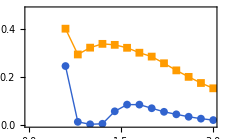

```mathematica
ListLinePlot[BfieldCLRad,BaseStyle->texStyle,Frame->True,PlotStyle->lineStyleLstDataThick⟦3;;-1⟧,PlotMarkers->{Automatic, 8},Axes->False,ImageSize->8cm,PlotRange->{{0,3},{0,0.48}},FrameLabel->{cRadiusLab⟦1⟧,xyLabNoDimLst⟦1,2⟧}]
```

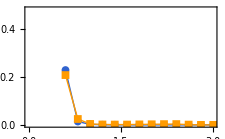

```mathematica
ListLinePlot[LinkCLRad,BaseStyle->texStyle,Frame->True,PlotStyle->lineStyleLstDataThick⟦3;;-1⟧,PlotMarkers->{Automatic, 8},Axes->False,ImageSize->8cm,PlotRange->{{0,3},{0,0.48}},FrameLabel->{cRadiusLab⟦1⟧,xyLabNoDimLst⟦2,2⟧}]
```

```mathematica
xyLabNoDimLst
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
BfieldCLNegWider=BfieldCLNeg;
```

```mathematica
LinkCLNegWider=LinkCLNeg;
```

```mathematica
BfieldCLNeg//Dimensions
```

{3,15,2}

```mathematica
BfieldCLNegWider//Dimensions
```

{3,15,2}

```mathematica
BfieldCLNegWider⟦All,All,1⟧
```

{{-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.},{-14.,-12.,-10.,-8.,-6.,-4.,-2.,0.,2.,4.,6.,8.,10.,12.,14.},{-21.,-18.,-15.,-12.,-9.,-6.,-3.,0.,3.,6.,9.,12.,15.,18.,21.}}

```mathematica
BfieldCLNegMerged={BfieldCLNeg⟦1⟧,BfieldCLNeg⟦2⟧~Join~BfieldCLNegWider⟦2⟧,BfieldCLNeg⟦3⟧~Join~BfieldCLNegWider⟦3⟧};
```

```mathematica
{BfieldCLNegMerged,linkCLNegMerged}=
((SortBy[#,First]&)/@Table[
If[iP==1,
#⟦1⟧⟦iP⟧,
#⟦1⟧⟦iP⟧~Join~#⟦2⟧⟦iP⟧
],
{iP,3}]&)/@{{BfieldCLNeg,BfieldCLNegWider},{LinkCLNeg,LinkCLNegWider}};
```

```mathematica
BfieldCLNegMergedSorted=SortBy[#,First]&/@BfieldCLNegMerged;
```

```mathematica
Dimensions/@BfieldCLNegMerged
```

{{15,2},{30,2},{30,2}}

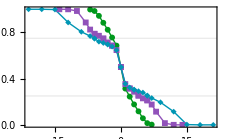

```mathematica
ListLinePlot[BfieldCLNegMerged,pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick⟦5;;-1⟧,PlotMarkers->{Automatic, 6},Axes->False,ImageSize->8cm,FrameLabel->{cALab⟦1⟧,xyLabNoDimLst⟦1,2⟧},GridLines->{None,{0.25,0.75}},GridLinesStyle->{Red,Dashed}]
```

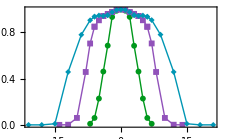

```mathematica
ListLinePlot[linkCLNegMerged,pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick⟦5;;-1⟧,PlotMarkers->{Automatic, 6},Axes->False,ImageSize->8cm,FrameLabel->{cALab⟦1⟧,xyLabNoDimLst⟦2,2⟧}]
```

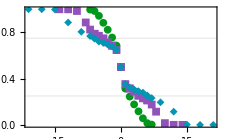

```mathematica
ListPlot[BfieldCLNegMerged,pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick⟦5;;-1⟧,PlotMarkers->{Automatic, 8},Axes->False,ImageSize->8cm,FrameLabel->{cALab⟦1⟧,xyLabNoDimLst⟦1,2⟧},GridLines->{None,{0.25,0.75}},GridLinesStyle->{Red,Dashed}]
```

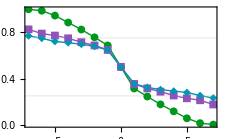

```mathematica
ListLinePlot[BfieldCLNeg,pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick⟦5;;-1⟧,PlotMarkers->{Automatic, 8},Axes->False,ImageSize->8cm,FrameLabel->{cALab⟦1⟧,xyLabNoDimLst⟦1,2⟧},GridLines->{None,{0.25,0.75}},GridLinesStyle->{Red,Dashed}]
```

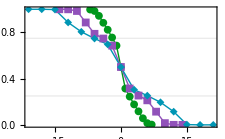

```mathematica
ListLinePlot[BfieldCLNeg,pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick⟦5;;-1⟧,PlotMarkers->{Automatic, 8},Axes->False,ImageSize->8cm,FrameLabel->{cALab⟦1⟧,xyLabNoDimLst⟦1,2⟧},GridLines->{None,{0.25,0.75}},GridLinesStyle->{Red,Dashed}]
```

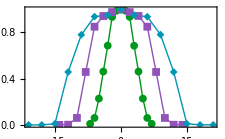

```mathematica
ListLinePlot[LinkCLNeg,pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick⟦5;;-1⟧,PlotMarkers->{Automatic, 8},Axes->False,ImageSize->8cm,FrameLabel->{cALab⟦1⟧,xyLabNoDimLst⟦2,2⟧}]
```

## Convergence check

### Adhoc testing

```mathematica
fNameLoopsNum="loopsNum_divNum_64_itNum_30000_cArea_1.0_cPerim_-1.0_beta_1_smart.jld2";
```

```mathematica
numBfieldLst=readJuliaVar[fNameLoopsNum,"numBfieldLst"];
```

```mathematica
numLinkLst=readJuliaVar[fNameLoopsNum,"numLinkLst"];
```

```mathematica
numLinkLst//Dimensions
```

{3,30000}

```mathematica
numBfieldLst//Dimensions
```

{3,30000}

```mathematica
bFieldLabLst=matexLstFunc[{"\\mathrm{iterations}","\\langle s \\rangle"},labMag];
```

```mathematica
bFieldLabLst
```

{-Graphics-,-Graphics-}

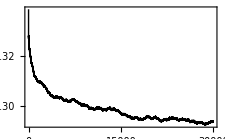

```mathematica
figBfieldHist=ListLinePlot[numBfieldLst⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->8cm,PlotRangePadding->None,PlotStyle->lineStyleLst,FrameLabel->bFieldLabLst]
```

```mathematica
linkLabLst=matexLstFunc[{"\\mathrm{iterations}","\\langle \ell \\rangle"},labMag];
```

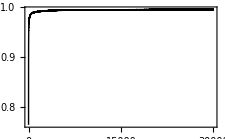

```mathematica
figLinkHist=ListLinePlot[numLinkLst⟦1⟧/64^3,PlotRange->All,PlotRange->Full,Frame->True,BaseStyle->texStyle,ImageSize->8cm,PlotRangePadding->None,PlotStyle->lineStyleLst,FrameLabel->linkLabLst]
```

```mathematica
Export["./figs/BfieldHistAB.pdf",figBfieldHist];
```

```mathematica
Export["./figs/linkHistAB.pdf",figLinkHist];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["./figs/BfieldHistAB.pdf"]]]
```

```mathematica
Directory[]
```

D:\Ohdraw.niL\OneDrive - UC San Diego\Programming\Julia\Modules

```mathematica
BfieldStartSampleLst=readJuliaVarDimFixed["loopsStartSample_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smartstaggeredCube.jld2","BfieldStartSampleLst"];
```

```mathematica
BfieldSampleLst=readJuliaVarSqDim["loopsSample_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smartstaggeredCube.jld2","BfieldSampleLst"];
```

```mathematica
BfieldSampleLst//Dimensions
```

{64,64,64,3,50}

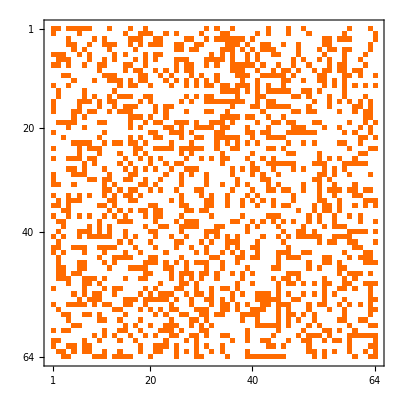

```mathematica
MatrixPlot[BfieldSampleLst⟦All,All,1,1,3⟧/.subBoolInt]
```

```mathematica
zakXTicks=Table[ii,{ii,0,1,0.2}];
zakYTicks=zakXTicks
```

{0.,0.2,0.4,0.6,0.8,1.}

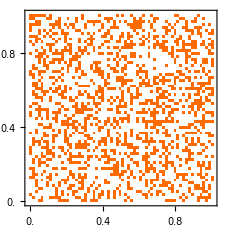

```mathematica
MatrixPlot[BfieldSampleLst⟦1,1,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

```mathematica
fNameLoopNum="loopsNum_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smartstaggeredCube.jld2";
```

```mathematica
numBfieldLst=readJuliaVarSqDim[fNameLoopNum,"numBfieldLst"];
```

```mathematica
numBfieldLst//Dimensions
```

{3,100}

```mathematica
numLinkLst=readJuliaVarSqDim[fNameLoopNum,"numLinkLst"];
```

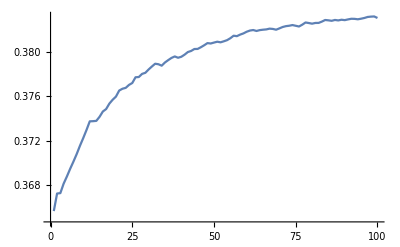

```mathematica
ListLinePlot[numBfieldLst⟦1⟧/64^3,PlotRange->All]
```

```mathematica
numLinkLst//Dimensions
```

{3,100}

```mathematica
64
```

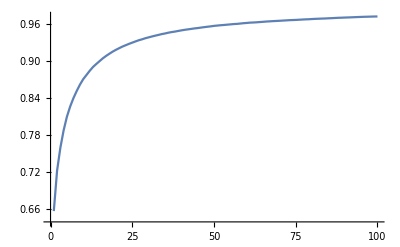

```mathematica
ListLinePlot[numLinkLst⟦1⟧/64^3,PlotRange->All]
```

```mathematica
fNameTest="loopsNum_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smart.jld2";
```

```mathematica
numLinkLstTest=readJuliaVarSqDim[fNameTest,"numLinkLst"];
```

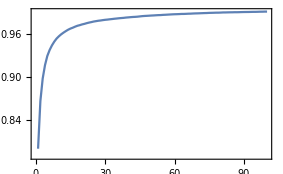

```mathematica
ListLinePlot[numLinkLstTest⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

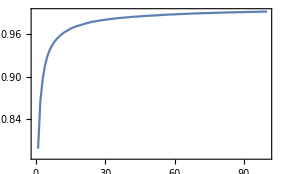

```mathematica
ListLinePlot[numLinkLstTest⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

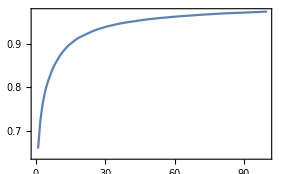

```mathematica
ListLinePlot[numLinkLstTest⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

```mathematica
fSampleNameBeta10="loopsSample_divNum_64_itNum_100_cArea_6.065306597126334_cPerim_-16.48721270700128_beta_1_smart.jld2";
```

```mathematica
BfieldSampleLstTest10Staggered=readJuliaVarSqDim[fSampleNameBeta10,"BfieldSampleLst"];
```

```mathematica
BfieldSampleLstTest=readJuliaVarSqDim["loopsSample_divNum_64_itNum_100_cArea_0.6065306597126334_cPerim_-1.6487212707001282_beta_1_smart.jld2","BfieldSampleLst"];
```

```mathematica
BfieldSampleLstTest10//Dimensions
```

{100,3,64,64,64}

```mathematica
Clear[BfieldSampleLstTest]
```

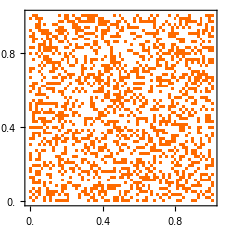

```mathematica
MatrixPlot[BfieldSampleLstTest⟦100,2,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

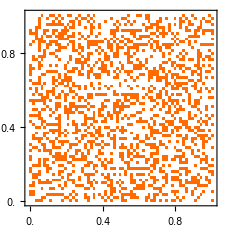

```mathematica
MatrixPlot[BfieldSampleLstTest⟦100,2,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

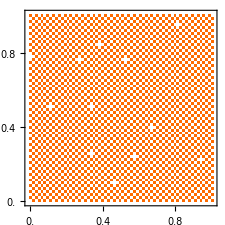

```mathematica
MatrixPlot[BfieldSampleLstTest10⟦100,1,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

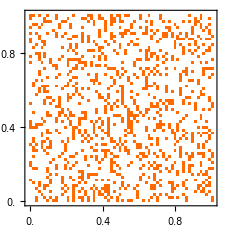

```mathematica
MatrixPlot[BfieldSampleLstTest10Staggered⟦10,3,All,All,1⟧/.subBoolInt,PlotRangePadding->None,ImageSize->8cm,BaseStyle->texStyle,DataRange->{{0,1},{0,1}},FrameTicks->{{zakXTicks,None},{zakYTicks,None}}]
```

```mathematica
fNameTest3="loopsNum_divNum_64_itNum_30000_cArea_1.0_cPerim_-1.0_beta_1_smart.jld2";
```

```mathematica
numLinkLstTestStg=readJuliaVarSqDim[fNameTest3,"numLinkLst"];
numBfieldLstTestStg=readJuliaVarSqDim[fNameTest3,"numBfieldLst"];
```

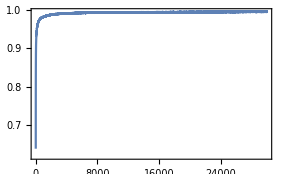

```mathematica
ListLinePlot[numLinkLstTestStg⟦1⟧/64^3,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

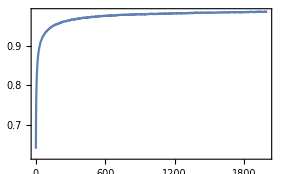

```mathematica
ListLinePlot[(numLinkLstTestStg⟦1⟧/64^3)⟦1;;2000⟧,PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

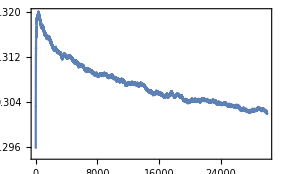

```mathematica
ListLinePlot[(numBfieldLstTestStg⟦1⟧/64^3),PlotRange->All,Frame->True,BaseStyle->texStyle,ImageSize->10cm]
```

### Filenames and variables loading

```mathematica
attrLstParamLst={"beta","cRatio","cFerroRatio","isInit0","sgnArea","sgnPerim"};
```

```mathematica
fNameFLstJld2=readTxtLastLine[dirLog<>fNameFLstLstJld2];
fNameParams=readTxtLastLine[dirLog<>fNameSaveParamLstLst];
```

```mathematica
fNameFLstJld2
```

loopsNum_Jld2Master_itNumLst_div_64_it_[200, 100]_isInit0_false_cRadius_[1, 1.2]_cAreas_-7_cAreas_-14_cAreas_-21_upStagCube.jld2

```mathematica
fNameParams
```

loopsMC_params_div_64_it_[200, 100]_isInit0_false_cRadius_[1, 1.2]_cAreas_-7_cAreas_-14_cAreas_-21_upStagCube.jld2

```mathematica
fNameFLstJld2Lst=readJuliaVar[fNameFLstJld2,"fLstNameLst"];
fNameArrLoopNumLst=Table[readJuliaVarDimRev[fNameFLstJld2Lst⟦iGrp⟧,"fNameArr"],{iGrp,Length[fNameFLstJld2Lst]}];
```

```mathematica
{itNumLst,divNumLst,isInit0Lst}=readJuliaVarDimRev[fNameParams,#]&/@{"itNumLst","divNumLst","isInit0Lst"};
{grpNameLst,grpParamsLst,grpParamsNameLst}=readJuliaVar[fNameParams,#]&/@{"grpNameLst","grpParamsLst","grpParamsNameLst"};
{cAreaLst,cPerimLst,cFerroLst}=
Module[{arrTmp=readJuliaVar[fNameParams,#]},
Table[
reverseDims[arrTmp⟦iGrp⟧]
,{iGrp,Length[grpNameLst]}]
]&/@{"cAreaLst","cPerimLst","cFerroLst"};
```

```mathematica
iGrpParamsLst=Table[Table[Subscript[iPrm, iGrp,iIt],{iIt,Length[grpParamsNameLst⟦iGrp⟧]}],{iGrp,Length[grpNameLst]}];
iGrpParamsBndLst=Table[Table[{Subscript[iPrm, iGrp,iIt],Length[grpParamsLst⟦iGrp,iIt⟧]},{iIt,Length[grpParamsNameLst⟦iGrp⟧]}],{iGrp,Length[grpNameLst]}];
```

```mathematica
iGrpParamsLst
```

{{iPrm_(1,1),iPrm_(1,2),iPrm_(1,3),iPrm_(1,4),iPrm_(1,5)},{iPrm_(2,1),iPrm_(2,2),iPrm_(2,3)}}

```mathematica
grpNameLst
```

{RadiusParamsGroup,CartesianParamsGroup}

```mathematica
fNameParamsOld=readTxtLastLine[dirLog<>fNameSaveParamLstLst];
```

```mathematica
fNameParamsOld
```

loopsMC_params_beta_[0.2, 10.0]_cRatio_[0.135, 7.389]_cFerroRatio_[0, 0]_isInit0_[false, true]_sgnArea_[1, -1]_sgnPerim_[1, -1]_stag.jld2

```mathematica
{cAreaLstOld,cPerimLstOld}=readJuliaVarDimFixed[fNameParamsOld,#]&/@{"cAreaLst","cPerimLst"};
```

```mathematica
nDim=3;
```

```mathematica
divNum=divNumLst⟦1⟧;
numGrd=divNum^nDim;
```

```mathematica
fNameFLstJld2Lst
```

{loopsNum_fLstJld2_div_64_it_100_isInit0_false_beta_3_cRatio_[0.135, 1]_cFerroRatio_0_sgnArea_1_sgnPerim_1_upStagCube.jld2}

```mathematica
grpNameLst
```

{BetaCRatioGroup,RadiusParamsGroup,CartesianParamsGroup}

```mathematica
grpParamsNameLst
```

{{beta,cRatio,cFerroRatio,sgnArea,sgnPerim},{cRadius,cAngle,cFerroRatio,sgnAreaLst,sgnPerimLst},{cAreas,cPerims,cFerros}}

```mathematica
fNameFLstJld2Lst
```

{loopsNum_fLstJld2_div_64_it_100_isInit0_false_beta_3_cRatio_[0.135, 1]_cFerroRatio_0_sgnArea_1_sgnPerim_1_upStagCube.jld2}

```mathematica
fNameArrLoopNum=readJuliaVar[fNameFLstJld2Lst⟦1⟧,"fNameArr"];
```

```mathematica
fNameFLstJld2
```

loopsNum_fLstJld2_div_64_it_100_isInit0_false_beta_3_cRatio_[0.135, 1]_cFerroRatio_0_sgnArea_1_sgnPerim_1_upStagCube.jld2

```mathematica
fNameParams
```

loopsMC_params_div_64_it_100_isInit0_false_beta_3_cRatio_[0.135, 1]_cFerroRatio_0_sgnArea_1_sgnPerim_1_upStagCube.jld2

```mathematica
itSampleNum=50;
```

```mathematica
divStep=1/divNum;
```

### Param points on the phase diagram

```mathematica
c2Lst=Table[Transpose[{cAreaLst⟦iGrp⟧,cPerimLst⟦iGrp⟧},{ArrayDepth[cAreaLst⟦iGrp⟧]+1}~Join~Range[1,ArrayDepth[cAreaLst⟦iGrp⟧]]],{iGrp,Length[grpNameLst]}];
```

```mathematica
c2Lst⟦1⟧//Dimensions
```

{15,4,1,1,1,2}

```mathematica
c2Lst⟦1,All,1,1,1,1⟧
```

{{0.190211,0.0618034},{0.380423,0.123607},{0.570634,0.18541},{0.760845,0.247214},{0.951057,0.309017},{1.14127,0.37082},{1.33148,0.432624},{1.52169,0.494427},{1.7119,0.556231},{1.90211,0.618034},{2.09232,0.679837},{2.28254,0.741641},{2.47275,0.803444},{2.66296,0.865248},{2.85317,0.927051}}

```mathematica
Transpose[list,m<->n]
```

```mathematica
c2LstTest=c2Lst⟦1,All,All,1,1,1⟧;
```

```mathematica
c2LstTest//Dimensions
```

{15,4,2}

```mathematica
Transpose[c2LstTest,1<->2]
```

{{{0.190211,0.0618034},{0.380423,0.123607},{0.570634,0.18541},{0.760845,0.247214},{0.951057,0.309017},{1.14127,0.37082},{1.33148,0.432624},{1.52169,0.494427},{1.7119,0.556231},{1.90211,0.618034},{2.09232,0.679837},{2.28254,0.741641},{2.47275,0.803444},{2.66296,0.865248},{2.85317,0.927051}},{{0.161803,0.117557},{0.323607,0.235114},{0.48541,0.352671},{0.647214,0.470228},{0.809017,0.587785},{0.97082,0.705342},{1.13262,0.822899},{1.29443,0.940456},{1.45623,1.05801},{1.61803,1.17557},{1.77984,1.29313},{1.94164,1.41068},{2.10344,1.52824},{2.26525,1.6458},{2.42705,1.76336}},{{0.117557,0.161803},{0.235114,0.323607},{0.352671,0.48541},{0.470228,0.647214},{0.587785,0.809017},{0.705342,0.97082},{0.822899,1.13262},{0.940456,1.29443},{1.05801,1.45623},{1.17557,1.61803},{1.29313,1.77984},{1.41068,1.94164},{1.52824,2.10344},{1.6458,2.26525},{1.76336,2.42705}},{{0.0618034,0.190211},{0.123607,0.380423},{0.18541,0.570634},{0.247214,0.760845},{0.309017,0.951057},{0.37082,1.14127},{0.432624,1.33148},{0.494427,1.52169},{0.556231,1.7119},{0.618034,1.90211},{0.679837,2.09232},{0.741641,2.28254},{0.803444,2.47275},{0.865248,2.66296},{0.927051,2.85317}}}

```mathematica
c2Lst⟦2⟧//Dimensions
```

{15,3,1,2}

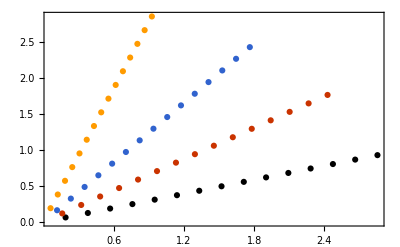

```mathematica
ListPlot[Transpose[c2Lst⟦1,All,All,1,1,1⟧,1<->2],pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick]
```

```mathematica
ListPlot[Transpose[c2Lst⟦1,All,All,1,1,1⟧,1<->2],pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick]
```

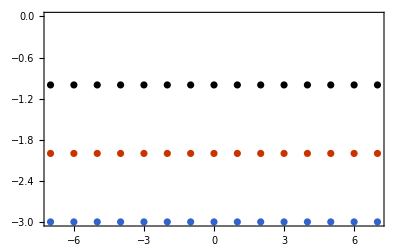

```mathematica
ListPlot[Transpose[c2Lst⟦2,All,All,1⟧,1<->2],pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick]
```

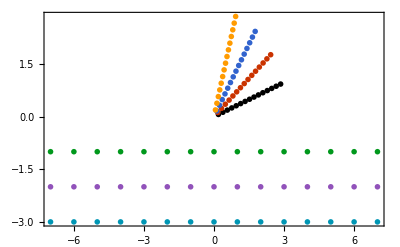

```mathematica
pltC2This=ListPlot[Transpose[c2Lst⟦1,All,All,1,1,1⟧,1<->2]~Join~Transpose[c2Lst⟦2,All,All,1⟧,1<->2],pltOptLstNoStyle,PlotStyle->markerStyleLstTmp]
```

```mathematica
c2dLstOld=Transpose[{cAreaLstOld,cPerimLstOld},{ArrayDepth[cAreaLstOld]+1}~Join~Range[1,ArrayDepth[cAreaLstOld]]];
```

```mathematica
c2dLstOld//Dimensions
```

{4,11,2,2,2}

```mathematica
lineStyleLstDataThick⟦1⟧
```

{GrayLevel[0],AbsoluteThickness[1]}

```mathematica
lineStyleLstDataThick⟦1⟧
```

{GrayLevel[0],AbsoluteThickness[1]}

```mathematica
c2dLstOld⟦1;;3,All,1,1⟧//Dimensions
```

{3,11,2}

```mathematica
PlotStyle->lineStyleLstDataThick⟦1⟧
```

PlotStyle→{GrayLevel[0],AbsoluteThickness[1]}

```mathematica
c2dLstOld⟦1;;3,All⟧//Dimensions
```

{3,11,2,2,2}

```mathematica
Flatten[c2dLstOld⟦1;;3,All⟧,{{2,3,4},{1}}]//Dimensions
```

{44,3,2}

```mathematica
lineStyleLstFunc[{Gray},dataThick]
```

{{GrayLevel[0.5],AbsoluteThickness[1]}}

```mathematica
c2dLstOld//Dimensions
```

{4,11,2,2,2}

```mathematica
c2dLstPhases={Flatten[c2dLstOld⟦1⟧,{Range[1,3]}],Flatten[c2dLstOld⟦2;;3,All,All,1⟧,{Range[1,3]}],Flatten[c2dLstOld⟦2,1;;-5,All,2⟧,{Range[1,2]}]~Join~Flatten[c2dLstOld⟦3,1;;-4,All,2⟧,{Range[1,2]}],Flatten[c2dLstOld⟦2,-4;;-1,2,2⟧,{1}]~Join~Flatten[c2dLstOld⟦3,-3;;-1,2,2⟧,{1}],Flatten[c2dLstOld⟦2,-4;;-1,1,2⟧,{1}]~Join~Flatten[c2dLstOld⟦3,-3;;-1,1,2⟧,{1}]};
```

```mathematica
Flatten[c2dLstOld⟦2,-4;;-1,2,2⟧,{1}]~Join~Flatten[c2dLstOld⟦3,-3;;-1,2,2⟧,{1}]
```

{{-1.49182,-0.67032},{-1.82212,-0.548812},{-2.22554,-0.449329},{-2.71828,-0.367879},{-5.46636,-1.64643},{-6.67662,-1.34799},{-8.15485,-1.10364}}

```mathematica
c2dLstPhases//Dimensions
```

{44,2}

```mathematica
xyLabscAcL=matexLstFunc[{"c_A","c_L"},labMag];
```

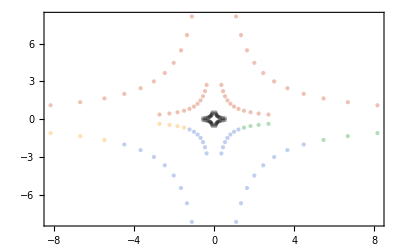

```mathematica
pltC2OldPhase=ListPlot[c2dLstPhases,pltOptLstNoStyle,PlotStyle->markerStyleLstOpac,FrameLabel->xyLabscAcL]
```

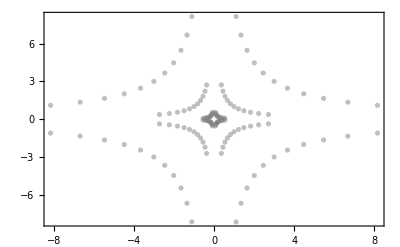

```mathematica
pltC2Old=ListPlot[Flatten[c2dLstOld⟦1;;3,All⟧,{{2,3,4},{1}}],pltOptLstNoStyle,PlotStyle->markerStyleLstFunc[{Opacity[0.5,Gray]},dataThick]]
```

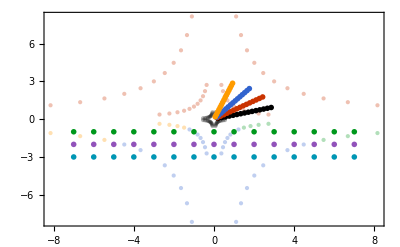

```mathematica
pltC2ThisOnOldPhase=Show[{pltC2OldPhase,pltC2This}]
```

```mathematica
Export[dirFigsDoc<>"c2ThisOnOldPhase.pdf",pltC2ThisOnOldPhase];
```

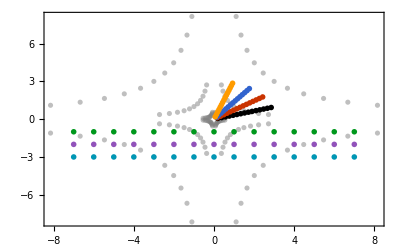

```mathematica
Show[{pltC2Old,pltC2This}]
```

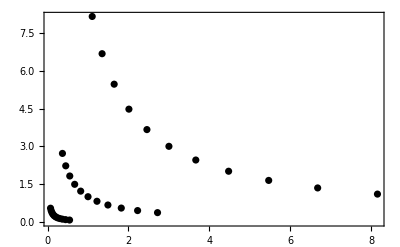

```mathematica
ListPlot[c2dLstOld⟦1;;3,All,1,1⟧,pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick⟦1;;1⟧]
```

```mathematica
c2dLstOld//Dimensions
```

{4,11,2,2,2}

```mathematica
c2dLstData=Transpose[c2dLst,{ArrayDepth[c2dLst]}~Join~Range[1,ArrayDepth[c2dLst]-1]];
```

```mathematica
c2dLstData//Dimensions
```

{4,11,1,2,2,2}

```mathematica
dimRatio=2;
```

```mathematica
c2dLstDataRatioRaw=Transpose[c2dLstData,{ArrayDepth[cAreaLst]-1}~Join~{ArrayDepth[cAreaLst]}~Join~Range[dimRatio-1,ArrayDepth[cAreaLst]-2]~Join~{ArrayDepth[c2dLst]}];
```

```mathematica
(*c2dLstDataRatio=ArrayReshape[c2dLstDataRatioRaw,{Times@@Dimensions[c2dLstDataRatioRaw]⟦1;;ArrayDepth[c2dLstDataRatioRaw]-2⟧}~Join~Dimensions[c2dLstDataRatioRaw]⟦-2;;-1⟧];*)
```

```mathematica
c2dLstDataRatio=Flatten[c2dLstDataRatioRaw,ArrayDepth[c2dLstDataRatioRaw]-3];
```

```mathematica
ArrayDepth[c2dLstDataRatioRaw]-3
```

3

```mathematica
c2dLstDataRatioRaw//Dimensions
```

{1,2,2,4,11,2}

```mathematica
c2dLstDataRatio//Dimensions
```

{16,11,2}

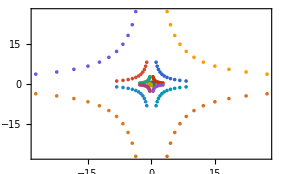

```mathematica
figcAcLMap=ListPlot[c2dLstDataRatio,PlotStyle->lineStyleLstDataThick,BaseStyle->texStyle,Frame->True,PlotRange->All,ImageSize->10cm,FrameLabel->xyLabscAcL]
```

```mathematica
c2dLstcAPcLPlFin=c2dLstData⟦1,All,1,1,1⟧;
```

```mathematica
c2dLstcAPcLPl0Raw=c2dLstData⟦2;;-1,All,1,1,1⟧;
```

```mathematica
c2dLstcAPcLPl0Raw=c2dLstData⟦2;;-1,All,1,1,1⟧;
```

```mathematica
c2dLstcAPcLPl0RawShort=c2dLstData⟦2;;3,All,1,1,1⟧;
```

```mathematica
c2dLstcAPcLPl0=Flatten[c2dLstcAPcLPl0Raw,ArrayDepth[c2dLstcAPcLPl0Raw]-2];
```

```mathematica
c2dLstcAPcLPl0Short=Flatten[c2dLstcAPcLPl0RawShort,ArrayDepth[c2dLstcAPcLPl0RawShort]-2];
```

```mathematica
c2dLstcANcLPlFin=c2dLstData⟦1,All,1,2,1⟧;
```

```mathematica
c2dLstcANcLPl0Raw=c2dLstData⟦2;;-1,All,1,2,1⟧;
```

```mathematica
c2dLstcANcLPl0RawShort=c2dLstData⟦2;;3,All,1,2,1⟧;
```

```mathematica
c2dLstcANcLPl0=Flatten[c2dLstcANcLPl0Raw,ArrayDepth[c2dLstcANcLPl0Raw]-2];
```

```mathematica
c2dLstcANcLPl0Short=Flatten[c2dLstcANcLPl0RawShort,ArrayDepth[c2dLstcANcLPl0RawShort]-2];
```

```mathematica
c2dLstcLPlFin=c2dLstcAPcLPlFin~Join~c2dLstcANcLPlFin;
```

```mathematica
c2dLstcLPlFin//Dimensions
```

{22,2}

```mathematica
c2dLstcLPl0=c2dLstcAPcLPl0~Join~c2dLstcANcLPl0;
```

```mathematica
c2dLstcLPl0Short=c2dLstcAPcLPl0Short~Join~c2dLstcANcLPl0Short;
```

```mathematica
c2dLstcLPl0//Dimensions
```

{66,2}

```mathematica
c2dLstcAPcLNlFin=c2dLstData⟦1,All,1,1,2⟧;
```

```mathematica
c2dLstcAPcLNlFin//Dimensions
```

{11,2}

```mathematica
c2dLstcAPcLNsSmall=c2dLstData⟦2,8;;-1,1,1,2⟧~Join~c2dLstData⟦3,9;;-1,1,1,2⟧~Join~c2dLstData⟦4,9;;-1,1,1,2⟧;
```

```mathematica
c2dLstcAPcLNsSmallShort=c2dLstData⟦2,8;;-1,1,1,2⟧~Join~c2dLstData⟦3,9;;-1,1,1,2⟧;
```

```mathematica
c2dLstcAPcLNlFull=c2dLstData⟦2,1;;7,1,1,2⟧~Join~c2dLstData⟦3,1;;8,1,1,2⟧~Join~c2dLstData⟦4,1;;8,1,1,2⟧;
```

```mathematica
c2dLstcAPcLNlFullShort=c2dLstData⟦2,1;;7,1,1,2⟧~Join~c2dLstData⟦3,1;;8,1,1,2⟧;
```

```mathematica
c2dLstcAPcLNl0Raw//Dimensions
```

{23,2}

```mathematica
c2dLstcANcLNlFin=c2dLstData⟦1,All,1,2,2⟧;
```

```mathematica
c2dLstcANcLNlFull=c2dLstData⟦2,1;;7,1,2,2⟧~Join~c2dLstData⟦3,1;;8,1,2,2⟧~Join~c2dLstData⟦4,1;;8,1,2,2⟧;
```

```mathematica
c2dLstcANcLNlFullShort=c2dLstData⟦2,1;;7,1,2,2⟧~Join~c2dLstData⟦3,1;;8,1,2,2⟧;
```

```mathematica
c2dLstcANcLNsLarge=c2dLstData⟦2,8;;-1,1,2,2⟧~Join~c2dLstData⟦3,9;;-1,1,2,2⟧~Join~c2dLstData⟦4,9;;-1,1,2,2⟧;
```

```mathematica
c2dLstcANcLNsLargeShort=c2dLstData⟦2,8;;-1,1,2,2⟧~Join~c2dLstData⟦3,9;;-1,1,2,2⟧;
```

```mathematica
c2dLstcLNlFin=c2dLstcAPcLNlFin~Join~c2dLstcANcLNlFin;
```

```mathematica
c2dLstcLNlFull=c2dLstcAPcLNlFull~Join~c2dLstcANcLNlFull;
```

```mathematica
c2dLstcLNlFullShort=c2dLstcAPcLNlFullShort~Join~c2dLstcANcLNlFullShort;
```

```mathematica
c2dLstlFin=c2dLstcLPlFin~Join~c2dLstcLNlFin;
```

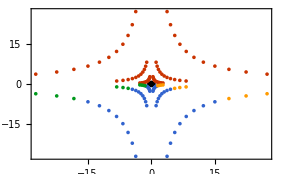

```mathematica
figcAcLPhaseSampleMap=ListPlot[{c2dLstlFin,c2dLstcLPl0,c2dLstcLNlFull,c2dLstcAPcLNsSmall,c2dLstcANcLNsLarge},PlotStyle->lineStyleLstDataThick,BaseStyle->texStyle,Frame->True,PlotRange->All,ImageSize->10cm,FrameLabel->xyLabscAcL]
```

```mathematica
legLstPhase=matexLstFunc[{"s, \\ell \\,\\, \\mathrm{finite}","s \\to 1","\\ell \\to 0", "\\ell \\to 1","s \\to 0"},labMag];
```

```mathematica
legLstPhase
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

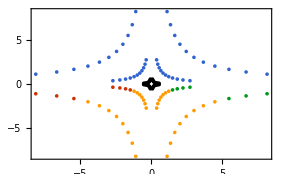

```mathematica
pltcAcLPhaseSample=ListPlot[{c2dLstlFin,c2dLstcANcLNsLargeShort,c2dLstcLPl0Short,c2dLstcLNlFullShort,c2dLstcAPcLNsSmallShort},PlotStyle->lineStyleLstDataThick,BaseStyle->texStyle,Frame->True,PlotRange->All,ImageSize->10cm,FrameLabel->xyLabscAcL,PlotLegends->legLstPhase]
```

```mathematica
Export[dirFigsDoc<>"cAcLPhaseSample.pdf",pltcAcLPhaseSample];
```

```mathematica
Placed[PointLegend[legLstPhase,Spacings->0.1],Scaled[{0.85,0.18}]]
```

```mathematica
c2dLstcAPcLPl0//Dimensions
```

{3,11,2}

```mathematica
c2dLstcAPcLPlFin
```

{{0.0735759,0.543656},{0.0898658,0.445108},{0.109762,0.364424},{0.134064,0.298365},{0.163746,0.244281},{0.2,0.2},{0.244281,0.163746},{0.298365,0.134064},{0.364424,0.109762},{0.445108,0.0898658},{0.543656,0.0735759}}

```mathematica
Export[dirFigsDoc<>"cAcLMap.pdf",figcAcLMap]
```

./figs/figsDoc/cAcLMap.pdf

```mathematica
c2dLstDataRatioRaw//Dimensions
```

{1,2,2,4,11,2}

```mathematica
iSgnArea=1;
iSgnPerim=2;
c2dLstDataSatLst=c2dLstDataRatioRaw⟦1,iSgnArea,iSgnPerim,2,1;;7⟧~Join~c2dLstDataRatioRaw⟦1,iSgnArea,iSgnPerim,3,1;;9⟧~Join~c2dLstDataRatioRaw⟦1,iSgnArea,iSgnPerim,4,1;;9⟧;
```

```mathematica
c2dLstDataNonSatLst=c2dLstDataRatioRaw⟦1,iSgnArea,iSgnPerim,1,All⟧~Join~c2dLstDataRatioRaw⟦1,iSgnArea,iSgnPerim,2,8;;-1⟧~Join~c2dLstDataRatioRaw⟦1,iSgnArea,iSgnPerim,3,10;;-1⟧~Join~c2dLstDataRatioRaw⟦1,iSgnArea,iSgnPerim,4,10;;-1⟧;
```

```mathematica
c2dLstDataSatLst//Dimensions
```

{25,2}

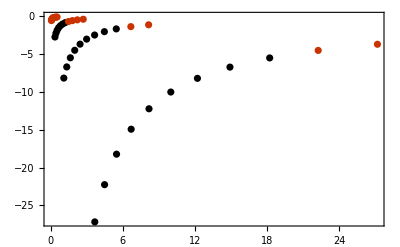

```mathematica
ListPlot[{c2dLstDataSatLst,c2dLstDataNonSatLst},PlotRange->All,BaseStyle->texStyle,Frame->True,PlotStyle->lineStyleLstDataThick,FrameLabel->xyLabscAcL]
```

```mathematica
iBeta=1;
iSgnArea=1;
iSgnPerim=1;
iCFerroRatio=1;
iInit0=1;
iDim=1;
fNameFigLstTmp=fNameFigBfieldJpgLst⟦1,1,iBeta,All,iCFerroRatio,iSgnArea,iSgnPerim,iInit0,iDim⟧;
```

```mathematica
fNameFigLstTmp//Dimensions
```

{11}

```mathematica
Export[dirFig<>"cAcLMap.pdf",figcAcLMap];
```

```mathematica
iGrpParamsBndLst⟦1⟧
```

{{iPrm_(1,1),1},{iPrm_(1,2),6},{iPrm_(1,3),1},{iPrm_(1,4),1},{iPrm_(1,5),1}}

```mathematica
fNameArrLoopNum⟦1,1,1,1⟧//Dimensions
```

{6,1,1,1,1}

```mathematica
iGrpParamsLst
```

{{iPrm_(1,1),iPrm_(1,2),iPrm_(1,3),iPrm_(1,4),iPrm_(1,5)},{iPrm_(2,1),iPrm_(2,2),iPrm_(2,3),iPrm_(2,4),iPrm_(2,5)},{iPrm_(3,1),iPrm_(3,2),iPrm_(3,3)}}

```mathematica
fNameArrLoopNumLst⟦3⟧//Dimensions
```

{1,1,1,1}

```mathematica
numBfieldLstArr=Table[Table[readJuliaVar[fNameArrLoopNumLst⟦iGrp⟧⟦iIt,iDiv,iInit,Sequence@@iGrpParamsLst⟦iGrp⟧⟧,"numBfieldLst"],{iDiv,1},{iIt,Length[itNumLst]},{iInit,Length[isInit0Lst]},Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧]],{iGrp,Length[grpNameLst]}];
```

```mathematica
numLinkLstArr=Table[Table[readJuliaVar[fNameArrLoopNumLst⟦iGrp⟧⟦iIt,iDiv,iInit,Evaluate@Sequence@@iGrpParamsLst⟦iGrp⟧⟧,"numLinkLst"],{iDiv,1},{iIt,Length[itNumLst]},{iInit,Length[isInit0Lst]},Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧]],{iGrp,Length[grpNameLst]}];
```

```mathematica
numBfieldLstArrBeta=Table[readJuliaVar[fNameArrLoopNum⟦iIt,iDiv,iBeta,iCRatio,iFerro,iSgnArea,iSgnPerim,iInit⟧,"numBfieldLst"],{iIt,1},{iDiv,1},{iBeta,Length[betaLst]},{iCRatio,Length[cRatioLst]},{iFerro,Length[cFerroRatioLst]},{iSgnArea,Length[sgnAreaLst]},{iSgnPerim,Length[sgnPerimLst]},{iInit,Length[isInit0Lst]}];
```

```mathematica
numLinkLstArrBeta=Table[readJuliaVar[fNameArrLoopNum⟦iIt,iDiv,iBeta,iCRatio,iCFerroRatio,iSgnArea,iSgnPerim,iInit⟧,"numLinkLst"],{iIt,1},{iDiv,1},{iBeta,Length[betaLst]},{iCRatio,1,Length[cRatioLst]},{iCFerroRatio,Length[cFerroRatioLst]},{iSgnArea,Length[sgnAreaLst]},{iSgnPerim,Length[sgnPerimLst]},{iInit,Length[isInit0Lst]}];
```

```mathematica
numBfieldLstArrBeta//Dimensions
```

{1,1,4,11,1,2,2,2,3,30000}

```mathematica
{numBfieldLstTotal,numLinkLstTotal}=Table[Map[Total,#⟦iGrp⟧,{ArrayDepth[#[[iGrp]]]-2}],{iGrp,Length[grpNameLst]}]&/@{numBfieldLstArr,numLinkLstArr};
```

```mathematica
{numBfieldLstTotalBeta,numLinkLstTotalBeta}=Map[Total,#⟦iGrp⟧,{ArrayDepth[#[[iGrp]]]-2}]&/@{numBfieldLstArrBeta,numLinkLstArrBeta};
```

```mathematica
numBfieldLstTotal⟦1⟧//Dimensions
```

{1,1,1,15,4,1,1,1,2000}

```mathematica
numLinkLstTotal⟦2⟧//Dimensions
```

{1,1,1,15,3,1,2000}

```mathematica
BfieldVsLinkArrBeta=Transpose[{numBfieldLstTotalBeta⟦iGrp⟧,numLinkLstTotalBeta⟦iGrp⟧},{ArrayDepth[numBfieldLstTotalBeta⟦iGrp⟧]+1}~Join~Range[1,ArrayDepth[numBfieldLstTotalBeta⟦iGrp⟧]]];
```

```mathematica
BfieldVsLinkLstBeta=Flatten[BfieldVsLinkArrBeta⟦iGrp⟧,ArrayDepth[BfieldVsLinkArrBeta⟦iGrp⟧]-2]/3/numGrd;
```

```mathematica
BfieldVsLinkLstBeta//Dimensions
```

{2640000,2}

```mathematica
BfieldVsLinkArrBeta//Dimensions
```

{4,11,1,2,2,2,30000,2}

```mathematica
BfieldVsLinkArr=Table[Transpose[{numBfieldLstTotal⟦iGrp⟧,numLinkLstTotal⟦iGrp⟧},{ArrayDepth[numBfieldLstTotal⟦iGrp⟧]+1}~Join~Range[1,ArrayDepth[numBfieldLstTotal⟦iGrp⟧]]],{iGrp,Length[grpNameLst]}];
```

```mathematica
BfieldVsLinkLst=Table[Flatten[BfieldVsLinkArr⟦iGrp⟧,ArrayDepth[BfieldVsLinkArr⟦iGrp⟧]-2]/3/numGrd,{iGrp,Length[grpNameLst]}];
```

```mathematica
BfieldVsLinkLst⟦2⟧//Dimensions
```

{90000,2}

```mathematica
pltSVsLTest=ListPlot[BfieldVsLinkLst⟦1⟧~Join~BfieldVsLinkLst⟦2⟧~Join~BfieldVsLinkLstBeta,PlotRange->All,pltOptMatPlot,ImageSize->10cm,FrameLabel->xyLabNoDimLst⟦All,2⟧];
```

```mathematica
Export[dirFigsDoc<>"sVsLTest.jpg",pltSVsLTest];
```

```mathematica
ListPlot[BfieldVsLinkLst⟦1⟧~Join~BfieldVsLinkLst⟦2⟧,PlotRange->All,pltOptMatPlot,ImageSize->10cm,FrameLabel->paramStrMatexLst⟦1;;2⟧]
```

-Graphics-

```mathematica
BfieldVsLinkLst⟦2⟧//Dimensions
```

{1,1,1,15,3,1,2000,2}

### MaTeX Labels generation

#### Axis label

```mathematica
itCut=10000;
```

```mathematica
itCut=-1;
```

```mathematica
varTrackedLstRaw={"s","\\ell"};
```

```mathematica
dimLabLst={"x","y","z"};
```

```mathematica
itLab="\\mathrm{iteration}";
```

```mathematica
xyLabNoDimLstRaw=Table[{itLab,"\\langle "<>varTrackedLstRaw⟦iBL⟧<>" \\rangle"},{iBL,2}];
```

```mathematica
xyLabNoDimLst=matexLstFunc[xyLabNoDimLstRaw,labMag];
```

```mathematica
xyLabNoDimLst
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
xyLabNoDimLst⟦All,2⟧
```

{-Graphics-,-Graphics-}

```mathematica
xyLabBLnkLstRaw=Table[{itLab,"\\langle "<>varTrackedLstRaw⟦iBL⟧<>"_"<>dimLabLst⟦iDim⟧<>" \\rangle"},{iBL,2},{iDim,nDim}];
```

```mathematica
xyLabBLnkLst=matexLstFunc[xyLabBLnkLstRaw,labMag];
```

```mathematica
xyLabBLnkLst
```

{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}

```mathematica
xyLabBLnkLst⟦All,All,2⟧
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

Test label output

```mathematica
xyLabNoDimLst
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
xyLabBLnkLst
```

{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}

```mathematica
xyLabThetaDimLstRaw=Table["\\theta"<>"_"<>dimLabLst⟦iDim⟧,{iDim,nDim}];
```

```mathematica
xyLabThetaDimNormedLstRaw=(#<>" / 2 \\pi") &/@xyLabThetaDimLstRaw;
```

```mathematica
xyLabThetaDimLst=matexLstFunc[xyLabThetaDimLstRaw,labMag];
```

```mathematica
xyLabThetaDimNormedLst=matexLstFunc[xyLabThetaDimNormedLstRaw,labMag];
```

```mathematica
xyLabThetaDimNormedLst
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
xyLabThetaDimLst
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
xyLabTheta2dLst=Table[Delete[xyLabThetaDimLst,iDim],{iDim,nDim}];
```

```mathematica
xyLabTheta2dNormedLst=Table[Delete[xyLabThetaDimNormedLst,iDim],{iDim,nDim}];
```

```mathematica
xyLabTheta2dNormedLst
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
xyLabTheta2dLst
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
cAreaLst//Dimensions
```

{2,15}

#### Title label

```mathematica
paramStrLst={"c_A","c_L", "c_F"};
```

```mathematica
paramStrMatexLst=matexLstFunc[paramStrLst,labMag];
```

```mathematica
titleFigLstRaw=Table[
Table[
Module[{valLst},
valLst={cAreaLst⟦iGrp⟧⟦##⟧,cPerimLst⟦iGrp⟧⟦##⟧,cFerroLst⟦iGrp⟧⟦##⟧}&@@iGrpParamsLst⟦iGrp⟧;
titleParamLstGen[paramStrLst,floatToStrWith0[#,numDigs]&/@valLst]
]
,Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧]]
,{iGrp,Length[grpNameLst]}];
```

```mathematica
cAreaLst//Dimensions
```

{2,15}

```mathematica
cAreaLst⟦1,1,1,1,1⟧⟦1⟧
```

0.190211

```mathematica
titleFigLstRaw
```

{{{{{{c_A=0.190\, ,\,c_L=0.062\, ,\,c_F=0}}},{{{c_A=0.162\, ,\,c_L=0.118\, ,\,c_F=0}}},{{{c_A=0.118\, ,\,c_L=0.162\, ,\,c_F=0}}},{{{c_A=0.062\, ,\,c_L=0.190\, ,\,c_F=0}}}},{{{{c_A=0.380\, ,\,c_L=0.124\, ,\,c_F=0}}},{{{c_A=0.324\, ,\,c_L=0.235\, ,\,c_F=0}}},{{{c_A=0.235\, ,\,c_L=0.324\, ,\,c_F=0}}},{{{c_A=0.124\, ,\,c_L=0.380\, ,\,c_F=0}}}},{{{{c_A=0.571\, ,\,c_L=0.185\, ,\,c_F=0}}},{{{c_A=0.485\, ,\,c_L=0.353\, ,\,c_F=0}}},{{{c_A=0.353\, ,\,c_L=0.485\, ,\,c_F=0}}},{{{c_A=0.185\, ,\,c_L=0.571\, ,\,c_F=0}}}},{{{{c_A=0.761\, ,\,c_L=0.247\, ,\,c_F=0}}},{{{c_A=0.647\, ,\,c_L=0.470\, ,\,c_F=0}}},{{{c_A=0.470\, ,\,c_L=0.647\, ,\,c_F=0}}},{{{c_A=0.247\, ,\,c_L=0.761\, ,\,c_F=0}}}},{{{{c_A=0.951\, ,\,c_L=0.309\, ,\,c_F=0}}},{{{c_A=0.809\, ,\,c_L=0.588\, ,\,c_F=0}}},{{{c_A=0.588\, ,\,c_L=0.809\, ,\,c_F=0}}},{{{c_A=0.309\, ,\,c_L=0.951\, ,\,c_F=0}}}},{{{{c_A=1.141\, ,\,c_L=0.371\, ,\,c_F=0}}},{{{c_A=0.971\, ,\,c_L=0.705\, ,\,c_F=0}}},{{{c_A=0.705\, ,\,c_L=0.971\, ,\,c_F=0}}},{{{c_A=0.371\, ,\,c_L=1.141\, ,\,c_F=0}}}},{{{{c_A=1.331\, ,\,c_L=0.433\, ,\,c_F=0}}},{{{c_A=1.133\, ,\,c_L=0.823\, ,\,c_F=0}}},{{{c_A=0.823\, ,\,c_L=1.133\, ,\,c_F=0}}},{{{c_A=0.433\, ,\,c_L=1.331\, ,\,c_F=0}}}},{{{{c_A=1.522\, ,\,c_L=0.494\, ,\,c_F=0}}},{{{c_A=1.294\, ,\,c_L=0.940\, ,\,c_F=0}}},{{{c_A=0.940\, ,\,c_L=1.294\, ,\,c_F=0}}},{{{c_A=0.494\, ,\,c_L=1.522\, ,\,c_F=0}}}},{{{{c_A=1.712\, ,\,c_L=0.556\, ,\,c_F=0}}},{{{c_A=1.456\, ,\,c_L=1.058\, ,\,c_F=0}}},{{{c_A=1.058\, ,\,c_L=1.456\, ,\,c_F=0}}},{{{c_A=0.556\, ,\,c_L=1.712\, ,\,c_F=0}}}},{{{{c_A=1.902\, ,\,c_L=0.618\, ,\,c_F=0}}},{{{c_A=1.618\, ,\,c_L=1.176\, ,\,c_F=0}}},{{{c_A=1.176\, ,\,c_L=1.618\, ,\,c_F=0}}},{{{c_A=0.618\, ,\,c_L=1.902\, ,\,c_F=0}}}},{{{{c_A=2.092\, ,\,c_L=0.680\, ,\,c_F=0}}},{{{c_A=1.780\, ,\,c_L=1.293\, ,\,c_F=0}}},{{{c_A=1.293\, ,\,c_L=1.780\, ,\,c_F=0}}},{{{c_A=0.680\, ,\,c_L=2.092\, ,\,c_F=0}}}},{{{{c_A=2.283\, ,\,c_L=0.742\, ,\,c_F=0}}},{{{c_A=1.942\, ,\,c_L=1.411\, ,\,c_F=0}}},{{{c_A=1.411\, ,\,c_L=1.942\, ,\,c_F=0}}},{{{c_A=0.742\, ,\,c_L=2.283\, ,\,c_F=0}}}},{{{{c_A=2.473\, ,\,c_L=0.803\, ,\,c_F=0}}},{{{c_A=2.103\, ,\,c_L=1.528\, ,\,c_F=0}}},{{{c_A=1.528\, ,\,c_L=2.103\, ,\,c_F=0}}},{{{c_A=0.803\, ,\,c_L=2.473\, ,\,c_F=0}}}},{{{{c_A=2.663\, ,\,c_L=0.865\, ,\,c_F=0}}},{{{c_A=2.265\, ,\,c_L=1.646\, ,\,c_F=0}}},{{{c_A=1.646\, ,\,c_L=2.265\, ,\,c_F=0}}},{{{c_A=0.865\, ,\,c_L=2.663\, ,\,c_F=0}}}},{{{{c_A=2.853\, ,\,c_L=0.927\, ,\,c_F=0}}},{{{c_A=2.427\, ,\,c_L=1.763\, ,\,c_F=0}}},{{{c_A=1.763\, ,\,c_L=2.427\, ,\,c_F=0}}},{{{c_A=0.927\, ,\,c_L=2.853\, ,\,c_F=0}}}}},{{{c_A=-7.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=-7.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=-7.000\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=-6.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=-6.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=-6.000\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=-5.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=-5.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=-5.000\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=-4.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=-4.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=-4.000\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=-3.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=-3.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=-3.000\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=-2.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=-2.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=-2.000\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=-1.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=-1.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=-1.000\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=0\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=0\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=0\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=1.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=1.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=1.000\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=2.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=2.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=2.000\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=3.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=3.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=3.000\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=4.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=4.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=4.000\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=5.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=5.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=5.000\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=6.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=6.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=6.000\, ,\,c_L=-3.000\, ,\,c_F=0}},{{c_A=7.000\, ,\,c_L=-1.000\, ,\,c_F=0},{c_A=7.000\, ,\,c_L=-2.000\, ,\,c_F=0},{c_A=7.000\, ,\,c_L=-3.000\, ,\,c_F=0}}}}

```mathematica
titleParamMatexLst=matexLstFunc[titleFigLstRaw,labMag];
```

```mathematica
titleParamMatexLst//Dimensions
```

{2,15}

```mathematica
titleParamMatexLst
```

{{{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}},{{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}},{{{-Graphics-}}}}},{{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}},{{-Graphics-},{-Graphics-},{-Graphics-}}}}

### Plotting starts

#### file naming

```mathematica
fMainLoopMCFig="loopsMC";
fMainLoopMCFigBfield=fMainLoopMCFig<>"Bfield";
fMainLoopMCFigLink=fMainLoopMCFig<>"Link";
fMainLoopMCFigBfLnk=fMainLoopMCFig<>"BfLnk";
fMainLoopMCFigBfieldAllDim=fMainLoopMCFigBfield<>"AllDim";
fMainLoopMCFigLinkAllDim=fMainLoopMCFigLink<>"AllDim";
```

```mathematica
fNamefNameFigLstTmp="fNameFigLstTmp.txt";
```

```mathematica
attrLstSimSetup={"itNum","divNum","isInit0"};
attrLstParams={"cArea","cPerim", "cFerro"};
attrLstBase=attrLstParams~Join~attrLstSimSetup;
attrLstItCut={"itCut"};
attrLstIDim={"iDim"};
```

```mathematica
(*attrLstLoopsMCFig={"cArea","cPerim", "cFerro", "isInit0","iDim","itCut"};*)
```

```mathematica
attrLstLoopsMCFig=attrLstBase~Join~attrLstIDim;
attrLstLoopsMCFigCut=attrLstBase~Join~attrLstIDim~Join~attrLstItCut;
```

#### Plot all

```mathematica
pltLstNumBfield=Table[
Table[ListPlot[numBfieldLstArr⟦iGrp⟧⟦iIt,iDiv,iInit,Evaluate@Sequence@@iGrpParamsLst⟦iGrp⟧,iDim⟧/numGrd,pltOptLstNoStyle,PlotStyle->markerStyleLstTmp,ImageSize->8cm,PlotLabel->titleParamMatexLst⟦iGrp⟧⟦Sequence@@iGrpParamsLst⟦iGrp⟧⟧,FrameLabel->xyLabBLnkLst⟦1,iDim⟧],{iDiv,1},{iIt,Length[itNumLst]},{iInit,Length[isInit0Lst]},Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧],{iDim,3}]
,{iGrp,Length[grpNameLst]}];
```

```mathematica
pltLstNumLink=Table[
Table[ListPlot[numLinkLstArr⟦iGrp⟧⟦iIt,iDiv,iInit,Evaluate@Sequence@@iGrpParamsLst⟦iGrp⟧,iDim⟧/numGrd,pltOptLstNoStyle,PlotStyle->markerStyleLstTmp,ImageSize->8cm,PlotLabel->titleParamMatexLst⟦iGrp⟧⟦Sequence@@iGrpParamsLst⟦iGrp⟧⟧,FrameLabel->xyLabBLnkLst⟦2,iDim⟧],{iDiv,1},{iIt,Length[itNumLst]},{iInit,Length[isInit0Lst]},Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧],{iDim,3}]
,{iGrp,Length[grpNameLst]}];
```

```mathematica
pltLstNumBfield⟦3⟧//Dimensions
```

{1,1,1,15,1,1,3}

```mathematica
pltLstNumBfield⟦3⟧//Dimensions
```

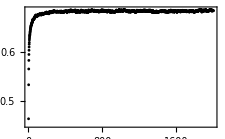

```mathematica
pltLstNumLink⟦2⟧⟦1,1,1,5,1,1,1⟧
```

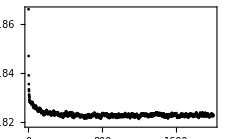

```mathematica
pltLstNumBfield⟦2⟧⟦1,1,1,5,1,1,1⟧
```

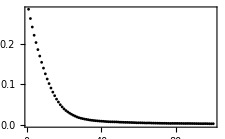

```mathematica
pltLstNumBfield⟦2⟧⟦1,1,1,1,2,1,1,1,1⟧
```

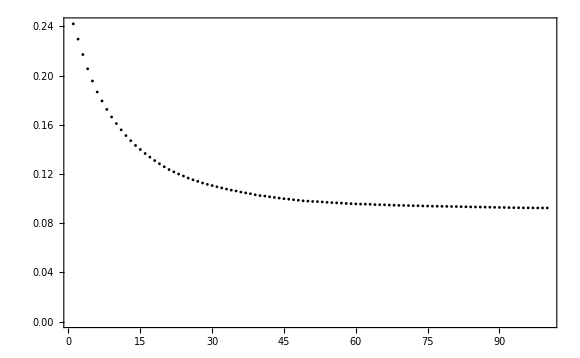

```mathematica
pltLstNumBfield⟦1⟧⟦1,1,1,1,1,1,1,1,1⟧
```

```mathematica
fNameFigNumBfieldJpgLst=Table[
Table[
Module[{valLst,fName},
valLst=(floatToStrWith0[#,numDigs]&/@({cAreaLst⟦iGrp,##⟧,cPerimLst⟦iGrp,##⟧,cFerroLst⟦iGrp,##⟧}&@@ iGrpParamsLst⟦iGrp⟧))~Join~{itNumLst⟦iIt⟧,divNumLst⟦iDiv⟧,isInit0Lst⟦iInit⟧}~Join~{iDim};
fNameFun[fMainLoopMCFigBfield,attrLstLoopsMCFig,valLst,jpgType]
],
{iIt,Length[itNumLst]},{iDiv,Length[divNumLst]},{iInit,Length[isInit0Lst]},Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧],{iDim,nDim}]
,{iGrp,Length[grpNameLst]}];
```

```mathematica
fNameFigNumLinkJpgLst=Table[
Table[
Module[{valLst,fName},
valLst=(floatToStrWith0[#,numDigs]&/@({cAreaLst⟦iGrp,##⟧,cPerimLst⟦iGrp,##⟧,cFerroLst⟦iGrp,##⟧}&@@ iGrpParamsLst⟦iGrp⟧))~Join~{itNumLst⟦iIt⟧,divNumLst⟦iDiv⟧,isInit0Lst⟦iInit⟧}~Join~{iDim};
fNameFun[fMainLoopMCFigLink,attrLstLoopsMCFig,valLst,jpgType]
],
{iIt,Length[itNumLst]},{iDiv,Length[divNumLst]},{iInit,Length[isInit0Lst]},Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧],{iDim,nDim}]
,{iGrp,Length[grpNameLst]}];
```

```mathematica
fNameFigNumLinkJpgLst⟦1⟧//Dimensions
```

{1,1,1,15,4,1,1,1,3}

```mathematica
fNameFigNumBfieldJpgLst⟦1⟧//Dimensions
```

{1,1,1,15,4,1,1,1,3}

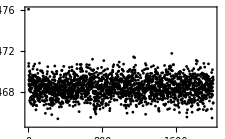

```mathematica
pltLstNumLink⟦1,1,1,1,1,1,1,1,1,1⟧
```

```mathematica
Do[
Do[
Export[dirFig<>fNameFigNumBfieldJpgLst⟦iGrp,iIt,iDiv,iInit,Sequence@@iGrpParamsLst⟦iGrp⟧,iDim⟧,pltLstNumBfield⟦iGrp,iIt,iDiv,iInit,Sequence@@iGrpParamsLst⟦iGrp⟧,iDim⟧]
,{iIt,Length[itNumLst]},{iDiv,Length[divNumLst]},{iInit,Length[isInit0Lst]},Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧],{iDim,nDim}]
,{iGrp,Length[grpNameLst]}]
```

```mathematica
{t1,b1}=AbsoluteTiming[
Do[
ParallelDo[
Export[dirFig<>fNameFigNumLinkJpgLst⟦iGrp,iIt,iDiv,iInit,Sequence@@iGrpParamsLst⟦iGrp⟧,iDim⟧,pltLstNumLink⟦iGrp,iIt,iDiv,iInit,Sequence@@iGrpParamsLst⟦iGrp⟧,iDim⟧]
,{iIt,Length[itNumLst]},{iDiv,Length[divNumLst]},{iInit,Length[isInit0Lst]},Evaluate[Sequence@@iGrpParamsBndLst⟦iGrp⟧]
,{iDim,nDim},DistributedContexts->Automatic]
,{iGrp,Length[grpNameLst]}]
];
t1
```

601.347

```mathematica
grpParamsLst⟦1,2⟧/π
```

{0.1,0.2,0.3,0.4}

```mathematica
Tan[0.1π]
```

0.32492

```mathematica
grpParamsLst⟦1,1⟧
```

{0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.}

```mathematica
0.062/0.19
```

0.326316

```mathematica
iGrp=1;
iAngle=3;
fNameLstFigTmp=fNameFigNumBfieldJpgLst[[iGrp,1,1,1,{5,6,12},iAngle,1,1,1,1]];
```

```mathematica
fNameLstFigTmp=fNameFigNumLinkJpgLst[[iGrp,1,1,1,All,iAngle,1,1,1,1]];
```

```mathematica
iGrp=2;
iCP=3;
iDim=1;
fNameLstFigTmp=fNameFigNumBfieldJpgLst⟦iGrp,1,1,1,All,iCP,1,iDim⟧;
```

```mathematica
fNameLstFigTmp=fNameFigNumLinkJpgLst[[iGrp,1,1,1,All,iCP,1,iDim]];
```

```mathematica
grpParamsNameLst⟦2⟧
```

{cAreas,cPerims,cFerros}

```mathematica
saveStrLstDelim[dirFig<>fNamefNameFigLstTmp,fNameLstFigTmp];
```

```mathematica
fNameLstFigTmp
```

{loopsMCBfield_cArea_-7.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_-6.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_-5.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_-4.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_-3.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_-2.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_-1.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_0_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_1.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_2.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_3.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_4.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_5.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_6.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg,loopsMCBfield_cArea_7.000_cPerim_-3.000_cFerro_0_itNum_2000_divNum_64_isInit0_False_iDim_1.jpg}

## <s>, <l> plots w.r.t. params

### Plotting params

```mathematica
itAvgStart=100;
iDim=1;
imgSz=8cm;
(*markerSz=AbsolutePointSize[7];*)
markerSz=7;
legMarkerSz=10;
```

### xyLabs

```mathematica
cRadiusLab=matexLstFunc[{"\\sqrt{c_A^2 + c_L^2}"},labMag];
```

```mathematica
cRadiusLab
```

{-Graphics-}

```mathematica
cALab=matexLstFunc[{"c_A"},labMag];
```

```mathematica
cALab
```

{-Graphics-}

```mathematica
grpParamsLst⟦2⟧
```

{{-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.},{-1.,-2.,-3.},{0.}}

```mathematica
ToString@@grpParamsLst⟦2,2⟧
```

ToString::nonopt: Options expected (instead of -3.) beyond position 2 in ToString[-1.,-2.,-3.]. An option must be a rule or a list of rules.

ToString[-1.,-2.,-3.]

```mathematica
ToString
```

```mathematica
legTitleCP=MaTeX["c_L=",Magnification->labMag];
```

```mathematica
legTitleCP
```

-Graphics-

```mathematica
legLabLstCP=matexLstFunc[ToString/@grpParamsLst⟦2,2⟧,labMag]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
angleLst=grpParamsLst⟦1,2⟧/π
```

{0.1,0.2,0.3,0.4}

```mathematica
legTitleAngle=MaTeX["\\tan^{-1} c_L / c_A =",Magnification->labMag]
```

-Graphics-

```mathematica
legLabLstAngle=matexLstFunc[ToString[#]<>"\\pi"&/@angleLst,labMag]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Plots

```mathematica
numBfieldLstArr//Dimensions
```

{2,1,1,1,15}

```mathematica
numBfieldLstArr⟦1⟧//Dimensions
```

{1,1,1,15,4,1,1,1,3,2000}

```mathematica
ArrayDepth[numBfieldLstArr⟦1⟧]-1
```

9

```mathematica
numBfieldLstArr⟦1⟧⟦1,1,1,1,1,1,1,1,1⟧//Dimensions
```

{2000}

```mathematica
numBfieldLstArrAvg=Map[Mean[#⟦-500;;-1⟧]&,numBfieldLstArr⟦1⟧,{ArrayDepth[numBfieldLstArr⟦1⟧]-1}];
```

```mathematica
numBfieldLstArrAvg=Table[Map[Mean[#⟦-itAvgStart;;-1⟧]&,numBfieldLstArr⟦iGrp⟧,{ArrayDepth[numBfieldLstArr⟦iGrp⟧]-1}],{iGrp,Length[grpNameLst]}];
```

```mathematica
numLinkLstArrAvg=Table[Map[Mean[#⟦-itAvgStart;;-1⟧]&,numLinkLstArr⟦iGrp⟧,{ArrayDepth[numLinkLstArr⟦iGrp⟧]-1}],{iGrp,Length[grpNameLst]}];
```

```mathematica
numBfieldLstArrAvg//Dimensions
```

{1,1,1,15,4,1,1,1,3}

```mathematica
grpParamsNameLst
```

{{cRadius,cAngle,cFerroRatio,sgnAreaLst,sgnPerimLst},{cAreas,cPerims,cFerros}}

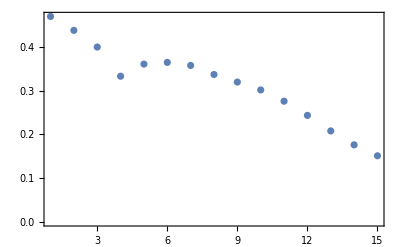

```mathematica
ListPlot[numBfieldLstArrAvg[[1,1,1,All,4,1,1,1,1]]/numGrd,pltOptLstNoStyle]
```

```mathematica
grpParamsLst⟦1⟧⟦1⟧
```

{0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.}

```mathematica
grpParamsLst⟦1⟧⟦1,{5,6,12}⟧
```

{1.,1.2,2.4}

```mathematica
xyLabBLnkLst
```

{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}

```mathematica
numBfieldAvgSliceRadius={grpParamsLst⟦1⟧⟦1⟧,#}ᵀ&/@(Transpose[numBfieldLstArrAvg⟦1⟧[[1,1,1,All,All,1,1,1,1]]]/numGrd);
```

```mathematica
numBfieldAvgSliceRadius//Dimensions
```

{4,15,2}

{0.1,0.2,0.3,0.4}

```mathematica
angl
```

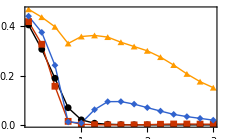

```mathematica
ListLinePlot[numBfieldAvgSliceRadius,pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick,PlotMarkers->{Automatic,markerSz},FrameLabel->{cRadiusLab⟦1⟧,xyLabBLnkLst⟦1,iDim,2⟧},ImageSize->imgSz,PlotLegends->Placed[LineLegend[legLabLstAngle,LegendMarkerSize->legMarkerSz,Spacings->0.3,LegendLabel->legTitleAngle],Scaled[{0.7,0.7}]]]
```

```mathematica
pltBfieldRadius=ListLinePlot[numBfieldAvgSliceRadius,pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick,PlotMarkers->{Automatic,markerSz},FrameLabel->{cRadiusLab⟦1⟧,xyLabBLnkLst⟦1,iDim,2⟧},ImageSize->imgSz,PlotLegends->Placed[LineLegend[legLabLstAngle,Spacings->0.1,LegendMarkerSize->legMarkerSz,LegendLayout->{"Column",2},LegendLabel->legTitleAngle],Scaled[{0.8,0.78}]]]
```

-Graphics-

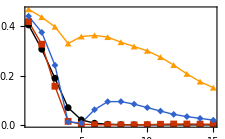

```mathematica
ListLinePlot[Transpose[numBfieldLstArrAvg⟦1⟧[[1,1,1,All,All,1,1,1,1]]]/numGrd,pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick,PlotMarkers->{Automatic,markerSz},FrameLabel->{cRadiusLab⟦1⟧,xyLabBLnkLst⟦1,iDim,2⟧},ImageSize->imgSz]
```

```mathematica
numLinkAvgSliceRadius={grpParamsLst⟦1⟧⟦1⟧,#}ᵀ&/@(Transpose[numLinkLstArrAvg⟦1⟧[[1,1,1,All,All,1,1,1,1]]]/numGrd);
```

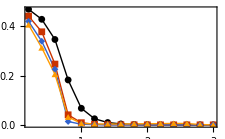

```mathematica
pltLinkRadius=ListLinePlot[numLinkAvgSliceRadius,pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick,PlotMarkers->{Automatic,markerSz},ImageSize->imgSz,FrameLabel->{cRadiusLab⟦1⟧,xyLabBLnkLst⟦2,iDim,2⟧},PlotLegends->Placed[LineLegend[legLabLstAngle,LegendMarkerSize->legMarkerSz,Spacings->0.3,LegendLabel->legTitleAngle],Scaled[{0.8,0.6}]]]
```

```mathematica
Export[dirFigsDoc<>"BfieldRadius.pdf",pltBfieldRadius]
```

./figs/figsDoc/BfieldRadius.pdf

```mathematica
Export[dirFigsDoc<>"linkRadius.pdf",pltLinkRadius]
```

./figs/figsDoc/linkRadius.pdf

```mathematica
{numBfieldAvgSliceCA,numLinkAvgSliceCA}=(({grpParamsLst⟦2⟧⟦1⟧,#}ᵀ&)/@(Transpose[#⟦2⟧[[1,1,1,All,All,1,iDim]]]/numGrd))&/@{numBfieldLstArrAvg,numLinkLstArrAvg};
```

```mathematica
markerSz
```

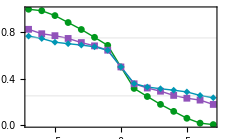

```mathematica
pltBfieldOnCAFixedCL=ListLinePlot[numBfieldAvgSliceCA,pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick⟦5;;-1⟧,PlotMarkers->{Automatic,markerSz},FrameLabel->{cALab⟦1⟧,xyLabBLnkLst⟦1,iDim,2⟧},Axes->False,ImageSize->imgSz,PlotLegends->Placed[LineLegend[legLabLstCP,LegendMarkerSize->legMarkerSz,Spacings->0.1,LegendLabel->legTitleCP],Scaled[{0.8,0.75}]],GridLines->{None,{0.25,0.75}},GridLinesStyle->{Red,Dashed}]
```

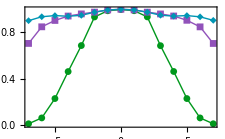

```mathematica
pltLinkOnCAFixedCL=ListLinePlot[numLinkAvgSliceCA,pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick⟦5;;-1⟧,PlotMarkers->{Automatic,markerSz},FrameLabel->{cALab⟦1⟧,xyLabBLnkLst⟦2,iDim,2⟧},Axes->False,ImageSize->imgSz,PlotLegends->Placed[LineLegend[legLabLstCP,LegendMarkerSize->legMarkerSz,Spacings->0.1,LegendLabel->legTitleCP],Scaled[{0.5,0.3}]]]
```

```mathematica
Export[dirFigsDoc<>"BfieldOnCAFixedCL.pdf",pltBfieldOnCAFixedCL];
Export[dirFigsDoc<>"linkOnCAFixedCL.pdf",pltLinkOnCAFixedCL];
```

## Misc

```mathematica
fNameTmp="loopsNum_div_64_it_100_nDim_3_cArea_1.414_BinomialInit_0.1956039178584847_cubeOnly_cAcLcFCubeFlip.jld2";
```

```mathematica
numBfieldArr=readJuliaVarDimRev[fNameTmp,"numBfieldLst"];
```

```mathematica
numLinkArr=readJuliaVarDimRev[fNameTmp,"numLinkLst"];
```

```mathematica
numBfieldArr//Dimensions
```

{100,3}

```mathematica
grd
```

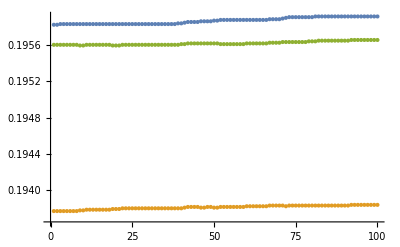

```mathematica
ListPlot[numBfieldArrᵀ/numGrdLst⟦1⟧]
```

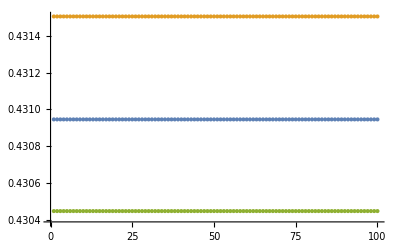

```mathematica
ListPlot[numLinkArrᵀ/numGrdLst⟦1⟧]
```